```mathematica
(*Mathematica*)
```

```mathematica
(* Dark enegy theory as a guage vector boson*)
```

```mathematica
(* 8 guage bosons in T(2,3) Teighmüller space:g#=3*3-3+3=9,genus 2 , 3 punctures*)
```

```mathematica
(* {H(0),Hbar(0),Z(0),W(+),W(+),γ,G(0),D(0)}:punctures are zero mass vector bosons, photon,graviton,dark vector boson ( called spirit boson)*)
```

```mathematica
(* dark vector boson perpendicular to the photon with six degrees freedom*)
```

```mathematica
(* solves to a particle with vector 24 states with three eigenvalues : SU(5) *)
```

```mathematica
(* hypothetical  equation for electron and positron : e(-)+e(+)->2*γ+2*D(0); two dark vector bosons (not observed or observable ,in complex  higher dimensions):dark energy would have to be less than 10^(-6) that of the electron to not be observed as an energy  "defect": why I call it "spirit"*)
```

```mathematica
(*photon electric vector field*)
```

```mathematica
a={a1,a2,a3,a4}
```

{a1,a2,a3,0}

```mathematica
(*dark boson vector field*)
```

```mathematica
d={d1,d2,d3,d4}
```

{d1,d2,d3,0}

```mathematica
g={1,1,1,-1}
```

{1,1,1,-1}

```mathematica
v={i,j,k,1}
```

{i,j,k,1}

```mathematica
m={a,d,g,v}
```

{{a1,a2,a3,0},{d1,d2,d3,0},{1,1,1,-1},{i,j,k,1}}

```mathematica
(*Minkowski Cross vectors of phton and dark boson*)
```

```mathematica
Cross[a,d,g]
```

{-a3 d2+a2 d3,a3 d1-a1 d3,-a2 d1+a1 d2,-a2 d1+a3 d1+a1 d2-a3 d2-a1 d3+a2 d3}

```mathematica
Det[m]
```

-a2 d1+a3 d1+a1 d2-a3 d2-a1 d3+a2 d3-a3 d2 i+a2 d3 i+a3 d1 j-a1 d3 j-a2 d1 k+a1 d2 k

```mathematica
a.d
```

a1 d1+a2 d2+a3 d3

```mathematica
(*3 orthgonal basis vector of a photon*)
```

```mathematica
ax={a1,0,0,a4}
ay={0,a2,0,a4}
az={0,0,a3,a4}
```

{a1,0,0,0}

{0,a2,0,0}

{0,0,a3,0}

```mathematica
(*3 orthgonal basis vector of a Dark boson*)
```

```mathematica
dx={d1,0,0,d4}
dy={0,d2,0,d4}
dz={0,0,d3,d4}
```

{d1,0,0,0}

{0,d2,0,0}

{0,0,d3,0}

```mathematica
(* 6 Dot interaction*)
```

```mathematica
ax.dy
ay.dz
az.dx
ay.dx
az.dy
ax.dz
```

0

0

0

«3 more identical outputs»

```mathematica
a4=0;d4=0;
```

```mathematica
(* 6 Cross inteactions*)
```

```mathematica
c[1]=mxy={ax,dy,g}
```

{{a1,0,0,0},{0,d2,0,0},{1,1,1,-1}}

```mathematica
c[2]=myz={ay,dz,g}
```

{{0,a2,0,0},{0,0,d3,0},{1,1,1,-1}}

```mathematica
c[3]=mzx={az,dx,g}
```

{{0,0,a3,0},{d1,0,0,0},{1,1,1,-1}}

```mathematica
c[4]=myx={ay,dx,g}
```

{{0,a2,0,0},{d1,0,0,0},{1,1,1,-1}}

```mathematica
c[5]=mzy={az,dy,g}
```

{{0,0,a3,0},{0,d2,0,0},{1,1,1,-1}}

```mathematica
c[6]=mxz={ax,dz,g}
```

{{a1,0,0,0},{0,0,d3,0},{1,1,1,-1}}

```mathematica
w=Table[Cross[c[i][[1]],c[i][[2]],c[i][[3]]],{i,6}]
```

{{0,0,a1 d2,a1 d2},{a2 d3,0,0,a2 d3},{0,a3 d1,0,a3 d1},{0,0,-a2 d1,-a2 d1},{-a3 d2,0,0,-a3 d2},{0,-a1 d3,0,-a1 d3}}

```mathematica
(*solving for dark vector in terms of photon vectors*)
```

```mathematica
d2/.Solve[Norm[w[[1]]]-1==0,{a1,d2}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{-1/(√2 a1),1/(√2 a1)}

```mathematica
d3/.Solve[Norm[w[[2]]]-1==0,{a2,d3}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{-1/(√2 a2),1/(√2 a2)}

```mathematica
d1/.Solve[Norm[w[[3]]]-1==0,{a3,d1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{-1/(√2 a3),1/(√2 a3)}

```mathematica
da={1/a1,1/a2,1/a3,0}*(1/Sqrt[2])
```

{1/(√2 a1),1/(√2 a2),1/(√2 a3),0}

```mathematica
dc=-{1/a1,1/a2,1/a3,0}*(1/Sqrt[2])
```

{-1/(√2 a1),-1/(√2 a2),-1/(√2 a3),0}

```mathematica
d1/.Solve[Norm[w[[4]]]-1==0,{a2,d1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{-1/(√2 a2),1/(√2 a2)}

```mathematica
d2/.Solve[Norm[w[[5]]]-1==0,{a3,d2}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{-1/(√2 a3),1/(√2 a3)}

```mathematica
d3/.Solve[Norm[w[[6]]]-1==0,{a1,d3}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{-1/(√2 a1),1/(√2 a1)}

```mathematica
(* 4 dark boson combined 4 vectors:a4=0;d4=0*)
```

```mathematica
db={1/a2,1/a3,1/a1,0}/Sqrt[2]
```

{1/(√2 a2),1/(√2 a3),1/(√2 a1),0}

```mathematica
dd=-{1/a2,1/a3,1/a1,0}/Sqrt[2]
```

{-1/(√2 a2),-1/(√2 a3),-1/(√2 a1),0}

```mathematica
(* 4 Cross product with photon in Minkowski space*)
```

```mathematica
ma=Cross[a,da,g]
```

{a2/(√2 a3)-a3/(√2 a2),-a1/(√2 a3)+a3/(√2 a1),a1/(√2 a2)-a2/(√2 a1),a1/(√2 a2)-a2/(√2 a1)-a1/(√2 a3)+a2/(√2 a3)+a3/(√2 a1)-a3/(√2 a2)}

```mathematica
mc=Cross[a,dc,g]
```

{-a2/(√2 a3)+a3/(√2 a2),a1/(√2 a3)-a3/(√2 a1),-a1/(√2 a2)+a2/(√2 a1),-a1/(√2 a2)+a2/(√2 a1)+a1/(√2 a3)-a2/(√2 a3)-a3/(√2 a1)+a3/(√2 a2)}

```mathematica
mb=Cross[a,dd,g]
```

{1/(√2)-a2/(√2 a1),1/(√2)-a3/(√2 a2),1/(√2)-a1/(√2 a3),3/(√2)-a2/(√2 a1)-a1/(√2 a3)-a3/(√2 a2)}

```mathematica
md=Cross[a,da,g]
```

{a2/(√2 a3)-a3/(√2 a2),-a1/(√2 a3)+a3/(√2 a1),a1/(√2 a2)-a2/(√2 a1),a1/(√2 a2)-a2/(√2 a1)-a1/(√2 a3)+a2/(√2 a3)+a3/(√2 a1)-a3/(√2 a2)}

```mathematica
Cross[ma,mc,mb]
```

{0,0,0,0}

```mathematica
Cross[ma,md,mb]
```

{0,0,0,0}

```mathematica
(* Cross vectors as perpendicular Normal vectors*)
```

```mathematica
ww=FullSimplify[ExpandAll[{Norm[ma]^2-1==0,Norm[mb]^2-1==0,Norm[mc]^2-1==0}]]
```

{Abs[a1/a2-a2/a1]^2+Abs[((a1-a2) (a1-a3) (a2-a3))/(a1 a2 a3)]^2+Abs[a1/a3-a3/a1]^2+Abs[a2/a3-a3/a2]^2==2,Abs[1-a2/a1]^2+Abs[1-a1/a3]^2+Abs[1-a3/a2]^2+Abs[-3+a2/a1+a1/a3+a3/a2]^2==2,Abs[a1/a2-a2/a1]^2+Abs[((a1-a2) (a1-a3) (a2-a3))/(a1 a2 a3)]^2+Abs[a1/a3-a3/a1]^2+Abs[a2/a3-a3/a2]^2==2}

```mathematica
(* removing the Absolute values to make solvable*)
```

```mathematica
ww1={(a1/a2-a2/a1)^2+(((a1-a2) (a1-a3) (a2-a3))/(a1 a2 a3))^2+(a1/a3-a3/a1)^2+(a2/a3-a3/a2)^2==2,(1-a2/a1)^2+(1-a1/a3)^2+(1-a3/a2)^2+(-3+a2/a1+a1/a3+a3/a2)^2==2,(a1/a2-a2/a1)^2+(((a1-a2) (a1-a3) (a2-a3))/(a1 a2 a3))^2+(a1/a3-a3/a1)^2+(a2/a3-a3/a2)^2==2}
```

{(a1/a2-a2/a1)^2+((a1-a2)^2 (a1-a3)^2 (a2-a3)^2)/(a1^2 a2^2 a3^2)+(a1/a3-a3/a1)^2+(a2/a3-a3/a2)^2==2,(1-a2/a1)^2+(1-a1/a3)^2+(1-a3/a2)^2+(-3+a2/a1+a1/a3+a3/a2)^2==2,(a1/a2-a2/a1)^2+((a1-a2)^2 (a1-a3)^2 (a2-a3)^2)/(a1^2 a2^2 a3^2)+(a1/a3-a3/a1)^2+(a2/a3-a3/a2)^2==2}

```mathematica
(* 24 solution vectors for 24 state dark vector boson*)
```

```mathematica
sol={a1,a2,a3}/.NSolve[ww1,{a1,a2,a3}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(69046 a1)/57903+(40299 a2)/38602-(142003 a3)/115806 == 1.

{{0.234388-0.297328 ⅈ,0.84414-0.615687 ⅈ,-0.324776-0.235038 ⅈ},{0.234388+0.297328 ⅈ,0.84414+0.615687 ⅈ,-0.324776+0.235038 ⅈ},{0.219231-0.193034 ⅈ,0.438927-0.676123 ⅈ,-0.655022-0.387914 ⅈ},{0.219231+0.193034 ⅈ,0.438927+0.676123 ⅈ,-0.655022+0.387914 ⅈ},{-0.470121-0.447188 ⅈ,0.704686-0.855176 ⅈ,0.241603-0.293199 ⅈ},{-0.470121+0.447188 ⅈ,0.704686+0.855176 ⅈ,0.241603+0.293199 ⅈ},{-0.187848-0.0719644 ⅈ,0.0997749-0.328743 ⅈ,-0.547898-0.209899 ⅈ},{-0.187848+0.0719644 ⅈ,0.0997749+0.328743 ⅈ,-0.547898+0.209899 ⅈ},{-0.417381-0.277666 ⅈ,0.278207-0.383054 ⅈ,-0.172775-0.0561017 ⅈ},{-0.417381+0.277666 ⅈ,0.278207+0.383054 ⅈ,-0.172775+0.0561017 ⅈ},{-0.0573303-0.479954 ⅈ,-0.450652+0.0727308 ⅈ,-1.14344+0.528657 ⅈ},{-0.0573303+0.479954 ⅈ,-0.450652-0.0727308 ⅈ,-1.14344-0.528657 ⅈ},{-0.327641-0.887894 ⅈ,-0.752972-2.04052 ⅈ,-1.13796-0.873798 ⅈ},{-0.327641+0.887894 ⅈ,-0.752972+2.04052 ⅈ,-1.13796+0.873798 ⅈ},{-0.560787-0.0839641 ⅈ,0.0971383-0.194687 ⅈ,-0.187476-0.0840993 ⅈ},{-0.560787+0.0839641 ⅈ,0.0971383+0.194687 ⅈ,-0.187476+0.0840993 ⅈ},{-0.518727-0.376404 ⅈ,-0.075848+0.233929 ⅈ,-0.375652+0.565198 ⅈ},{-0.518727+0.376404 ⅈ,-0.075848-0.233929 ⅈ,-0.375652-0.565198 ⅈ},{-0.423573-0.121119 ⅈ,-0.27897+0.0814097 ⅈ,-0.641118+0.187092 ⅈ},{-0.423573+0.121119 ⅈ,-0.27897-0.0814097 ⅈ,-0.641118-0.187092 ⅈ},{-0.682708-0.552107 ⅈ,-0.234068-0.189291 ⅈ,-0.350891+0.375745 ⅈ},{-0.682708+0.552107 ⅈ,-0.234068+0.189291 ⅈ,-0.350891-0.375745 ⅈ},{-0.792779-0.254607 ⅈ,-0.352831-0.420947 ⅈ,-0.344963-0.110787 ⅈ},{-0.792779+0.254607 ⅈ,-0.352831+0.420947 ⅈ,-0.344963+0.110787 ⅈ}}

```mathematica
Table[Norm[sol[[i]]],{i,24}]
```

{1.1814,1.1814,1.14658,1.14658,1.33912,1.33912,0.709044,0.709044,0.713046,0.713046,1.42441,1.42441,2.77216,2.77216,0.641163,0.641163,0.965296,0.965296,0.851217,0.851217,1.06106,1.06106,1.06126,1.06126}

```mathematica
Abs[{{0.23438795768745826-0.2973281544121372 ⅈ,0.8441395256354756-0.6156869604116004 ⅈ,-0.32477599502985427-0.23503775944029637 ⅈ},{0.23438795768745826+0.2973281544121372 ⅈ,0.8441395256354756+0.6156869604116004 ⅈ,-0.32477599502985427+0.23503775944029637 ⅈ},{0.21923076792044113-0.1930337356941755 ⅈ,0.43892686513536605-0.6761234546648848 ⅈ,-0.655021893828998-0.38791351358168835 ⅈ},{0.21923076792044113+0.1930337356941755 ⅈ,0.43892686513536605+0.6761234546648848 ⅈ,-0.655021893828998+0.38791351358168835 ⅈ},{-0.470120988272442-0.4471878576274256 ⅈ,0.7046858881962628-0.8551756675739393 ⅈ,0.24160304597636417-0.2931987848651091 ⅈ},{-0.470120988272442+0.4471878576274256 ⅈ,0.7046858881962628+0.8551756675739393 ⅈ,0.24160304597636417+0.2931987848651091 ⅈ},{-0.18784808143689685-0.0719643964169099 ⅈ,0.09977488275448423-0.32874288482556724 ⅈ,-0.5478982749508613-0.20989923534539892 ⅈ},{-0.18784808143689685+0.0719643964169099 ⅈ,0.09977488275448423+0.32874288482556724 ⅈ,-0.5478982749508613+0.20989923534539892 ⅈ},{-0.4173814412032934-0.27766629627906286 ⅈ,0.2782071311072794-0.3830541670411783 ⅈ,-0.17277490258570632-0.056101670014076996 ⅈ},{-0.4173814412032934+0.27766629627906286 ⅈ,0.2782071311072794+0.3830541670411783 ⅈ,-0.17277490258570632+0.056101670014076996 ⅈ},{-0.057330272614507564-0.4799544612688476 ⅈ,-0.45065195591358786+0.07273081897791575 ⅈ,-1.1434379379886512+0.5286565022394653 ⅈ},{-0.057330272614507564+0.4799544612688476 ⅈ,-0.45065195591358786-0.07273081897791575 ⅈ,-1.1434379379886512-0.5286565022394653 ⅈ},{-0.32764125353711215-0.8878937710470335 ⅈ,-0.7529721111853611-2.040522187227831 ⅈ,-1.1379578835836546-0.8737983298793416 ⅈ},{-0.32764125353711215+0.8878937710470335 ⅈ,-0.7529721111853611+2.040522187227831 ⅈ,-1.1379578835836546+0.8737983298793416 ⅈ},{-0.5607867356135836-0.08396410138582966 ⅈ,0.09713833148054289-0.1946874093036634 ⅈ,-0.18747565364566812-0.08409930095852203 ⅈ},{-0.5607867356135836+0.08396410138582966 ⅈ,0.09713833148054289+0.1946874093036634 ⅈ,-0.18747565364566812+0.08409930095852203 ⅈ},{-0.5187270072304172-0.376404400103709 ⅈ,-0.07584804519957064+0.2339292127888023 ⅈ,-0.37565228367027265+0.5651977525661375 ⅈ},{-0.5187270072304172+0.376404400103709 ⅈ,-0.07584804519957064-0.2339292127888023 ⅈ,-0.37565228367027265-0.5651977525661375 ⅈ},{-0.42357278393867814-0.12111857768531233 ⅈ,-0.2789698856365055+0.08140966814800024 ⅈ,-0.6411175072648934+0.18709246480573605 ⅈ},{-0.42357278393867814+0.12111857768531233 ⅈ,-0.2789698856365055-0.08140966814800024 ⅈ,-0.6411175072648934-0.18709246480573605 ⅈ},{-0.6827075591137881-0.5521073138012946 ⅈ,-0.23406772940377246-0.18929115930170337 ⅈ,-0.3508914179882584+0.3757446666010602 ⅈ},{-0.6827075591137881+0.5521073138012946 ⅈ,-0.23406772940377246+0.18929115930170337 ⅈ,-0.3508914179882584-0.3757446666010602 ⅈ},{-0.792779199897269-0.25460682275254165 ⅈ,-0.3528307618484336-0.4209474607517396 ⅈ,-0.3449625384180363-0.11078723544544192 ⅈ},{-0.792779199897269+0.25460682275254165 ⅈ,-0.3528307618484336+0.4209474607517396 ⅈ,-0.3449625384180363+0.11078723544544192 ⅈ}}]
```

{{0.378605,1.04482,0.400902},{0.378605,1.04482,0.400902},{0.292103,0.806102,0.761269},{0.292103,0.806102,0.761269},{0.648838,1.10811,0.379918},{0.648838,1.10811,0.379918},{0.201161,0.34355,0.586728},{0.201161,0.34355,0.586728},{0.501304,0.473423,0.181655},{0.501304,0.473423,0.181655},{0.483366,0.456483,1.25973},{0.483366,0.456483,1.25973},{0.946416,2.17502,1.43474},{0.946416,2.17502,1.43474},{0.567038,0.217575,0.205475},{0.567038,0.217575,0.205475},{0.640904,0.245918,0.678648},{0.640904,0.245918,0.678648},{0.440549,0.290606,0.667859},{0.440549,0.290606,0.667859},{0.878016,0.30103,0.51411},{0.878016,0.30103,0.51411},{0.83266,0.54926,0.362316},{0.83266,0.54926,0.362316}}

```mathematica
Max[Norm[%]]
```

5.89205

```mathematica
Length[sol]
```

24

```mathematica
re=Apply[Plus,Table[Norm[Re[sol[[i]]]],{i,24}]]/24
```

0.848625

```mathematica
im=Apply[Plus,Table[Norm[Im[sol[[i]]]],{i,24}]]/24
```

0.741513

```mathematica
re-im
```

0.107113

```mathematica
ga=ListPointPlot3D[Abs[sol],PlotStyle->Red]
```

-Graphics3D-

```mathematica
gr=ListPointPlot3D[Re[sol],PlotStyle->Blue]
```

-Graphics3D-

```mathematica
gi=ListPointPlot3D[Im[sol],PlotStyle->Yellow]
```

-Graphics3D-

```mathematica
Show[{ga,gr,gi},ImageSize->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
(* Using the solutions as a Killing vector decomposition of the 24 vertex group*)
```

```mathematica
solt=Transpose[sol]
```

{{0.234388-0.297328 ⅈ,0.234388+0.297328 ⅈ,0.219231-0.193034 ⅈ,0.219231+0.193034 ⅈ,-0.470121-0.447188 ⅈ,-0.470121+0.447188 ⅈ,-0.187848-0.0719644 ⅈ,-0.187848+0.0719644 ⅈ,-0.417381-0.277666 ⅈ,-0.417381+0.277666 ⅈ,-0.0573303-0.479954 ⅈ,-0.0573303+0.479954 ⅈ,-0.327641-0.887894 ⅈ,-0.327641+0.887894 ⅈ,-0.560787-0.0839641 ⅈ,-0.560787+0.0839641 ⅈ,-0.518727-0.376404 ⅈ,-0.518727+0.376404 ⅈ,-0.423573-0.121119 ⅈ,-0.423573+0.121119 ⅈ,-0.682708-0.552107 ⅈ,-0.682708+0.552107 ⅈ,-0.792779-0.254607 ⅈ,-0.792779+0.254607 ⅈ},{0.84414-0.615687 ⅈ,0.84414+0.615687 ⅈ,0.438927-0.676123 ⅈ,0.438927+0.676123 ⅈ,0.704686-0.855176 ⅈ,0.704686+0.855176 ⅈ,0.0997749-0.328743 ⅈ,0.0997749+0.328743 ⅈ,0.278207-0.383054 ⅈ,0.278207+0.383054 ⅈ,-0.450652+0.0727308 ⅈ,-0.450652-0.0727308 ⅈ,-0.752972-2.04052 ⅈ,-0.752972+2.04052 ⅈ,0.0971383-0.194687 ⅈ,0.0971383+0.194687 ⅈ,-0.075848+0.233929 ⅈ,-0.075848-0.233929 ⅈ,-0.27897+0.0814097 ⅈ,-0.27897-0.0814097 ⅈ,-0.234068-0.189291 ⅈ,-0.234068+0.189291 ⅈ,-0.352831-0.420947 ⅈ,-0.352831+0.420947 ⅈ},{-0.324776-0.235038 ⅈ,-0.324776+0.235038 ⅈ,-0.655022-0.387914 ⅈ,-0.655022+0.387914 ⅈ,0.241603-0.293199 ⅈ,0.241603+0.293199 ⅈ,-0.547898-0.209899 ⅈ,-0.547898+0.209899 ⅈ,-0.172775-0.0561017 ⅈ,-0.172775+0.0561017 ⅈ,-1.14344+0.528657 ⅈ,-1.14344-0.528657 ⅈ,-1.13796-0.873798 ⅈ,-1.13796+0.873798 ⅈ,-0.187476-0.0840993 ⅈ,-0.187476+0.0840993 ⅈ,-0.375652+0.565198 ⅈ,-0.375652-0.565198 ⅈ,-0.641118+0.187092 ⅈ,-0.641118-0.187092 ⅈ,-0.350891+0.375745 ⅈ,-0.350891-0.375745 ⅈ,-0.344963-0.110787 ⅈ,-0.344963+0.110787 ⅈ}}

```mathematica
ss1=sol.solt
```

{{0.350271-1.02616 ⅈ,1.39571+0. ⅈ,0.0697869-0.671472 ⅈ,1.19949+0.308532 ⅈ,-0.322199-1.08235 ⅈ,1.13459+0.380608 ⅈ,-0.0549952-0.103003 ⅈ,0.491273+0.349401 ⅈ,-0.138456-0.376793 ⅈ,0.524715+0.363632 ⅈ,0.00384022+0.340462 ⅈ,-0.0488191+0.786053 ⅈ,-2.06852-0.818333 ⅈ,1.38287+2.47528 ⅈ,-0.153154-0.00571534 ⅈ,0.176042+0.307705 ⅈ,0.101348+0.214905 ⅈ,-0.228561+0.363542 ⅈ,-0.0684656+0.427954 ⅈ,-0.184635+0.468816 ⅈ,-0.43603+0.0183451 ⅈ,-0.0512562+0.840802 ⅈ,-0.732534+0.154994 ⅈ,-0.0107079+0.913062 ⅈ},{1.39571+0. ⅈ,0.350271+1.02616 ⅈ,1.19949-0.308532 ⅈ,0.0697869+0.671472 ⅈ,1.13459-0.380608 ⅈ,-0.322199+1.08235 ⅈ,0.491273-0.349401 ⅈ,-0.0549952+0.103003 ⅈ,0.524715-0.363632 ⅈ,-0.138456+0.376793 ⅈ,-0.0488191-0.786053 ⅈ,0.00384022-0.340462 ⅈ,1.38287-2.47528 ⅈ,-2.06852+0.818333 ⅈ,0.176042-0.307705 ⅈ,-0.153154+0.00571534 ⅈ,-0.228561-0.363542 ⅈ,0.101348-0.214905 ⅈ,-0.184635-0.468816 ⅈ,-0.0684656-0.427954 ⅈ,-0.0512562-0.840802 ⅈ,-0.43603-0.0183451 ⅈ,-0.0107079-0.913062 ⅈ,-0.732534-0.154994 ⅈ},{0.0697869-0.671472 ⅈ,1.19949-0.308532 ⅈ,0.0248908-0.169992 ⅈ,1.31465+0. ⅈ,-0.730277-0.760772 ⅈ,0.826248-0.198081 ⅈ,0.0439121+0.158756 ⅈ,0.679082+0.20392 ⅈ,-0.190572-0.23277 ⅈ,0.478135+0.151746 ⅈ,0.700206+0.339739 ⅈ,0.377004+1.1789 ⅈ,-1.54694+0.495841 ⅈ,2.23306+1.53171 ⅈ,-0.137968+0.0665234 ⅈ,0.222959+0.164072 ⅈ,0.403802-0.0529235 ⅈ,-0.205706+0.647194 ⅈ,0.308877+0.40571 ⅈ,0.1004+0.63245 ⅈ,-0.111371-0.0240851 ⅈ,0.0662355+0.876405 ⅈ,-0.479447+0.357391 ⅈ,0.274026+0.693421 ⅈ},{1.19949+0.308532 ⅈ,0.0697869+0.671472 ⅈ,1.31465+0. ⅈ,0.0248908+0.169992 ⅈ,0.826248+0.198081 ⅈ,-0.730277+0.760772 ⅈ,0.679082-0.20392 ⅈ,0.0439121-0.158756 ⅈ,0.478135-0.151746 ⅈ,-0.190572+0.23277 ⅈ,0.377004-1.1789 ⅈ,0.700206-0.339739 ⅈ,2.23306-1.53171 ⅈ,-1.54694-0.495841 ⅈ,0.222959-0.164072 ⅈ,-0.137968-0.0665234 ⅈ,-0.205706-0.647194 ⅈ,0.403802+0.0529235 ⅈ,0.1004-0.63245 ⅈ,0.308877-0.40571 ⅈ,0.0662355-0.876405 ⅈ,-0.111371+0.0240851 ⅈ,0.274026-0.693421 ⅈ,-0.479447-0.357391 ⅈ},{-0.322199-1.08235 ⅈ,1.13459-0.380608 ⅈ,-0.730277-0.760772 ⅈ,0.826248+0.198081 ⅈ,-0.2413-0.926471 ⅈ,1.79324+0. ⅈ,-0.348609-0.0892194 ⅈ,0.401104+0.407862 ⅈ,-0.117671-0.153561 ⅈ,0.818722+0.15234 ⅈ,-0.564305+1.15089 ⅈ,-0.569443+0.341665 ⅈ,-3.04977-0.107534 ⅈ,1.74674+2.35571 ⅈ,0.0580975+0.104635 ⅈ,0.515492+0.340713 ⅈ,0.297099+0.885328 ⅈ,-0.0977857-0.0713831 ⅈ,-0.0820395+0.77547 ⅈ,-0.222664+0.456449 ⅈ,-0.227371+0.825296 ⅈ,0.369839+0.391401 ⅈ,-0.465601+0.55369 ⅈ,0.547047+0.961102 ⅈ},{1.13459+0.380608 ⅈ,-0.322199+1.08235 ⅈ,0.826248-0.198081 ⅈ,-0.730277+0.760772 ⅈ,1.79324+0. ⅈ,-0.2413+0.926471 ⅈ,0.401104-0.407862 ⅈ,-0.348609+0.0892194 ⅈ,0.818722-0.15234 ⅈ,-0.117671+0.153561 ⅈ,-0.569443-0.341665 ⅈ,-0.564305-1.15089 ⅈ,1.74674-2.35571 ⅈ,-3.04977+0.107534 ⅈ,0.515492-0.340713 ⅈ,0.0580975-0.104635 ⅈ,-0.0977857+0.0713831 ⅈ,0.297099-0.885328 ⅈ,-0.222664-0.456449 ⅈ,-0.0820395-0.77547 ⅈ,0.369839-0.391401 ⅈ,-0.227371-0.825296 ⅈ,0.547047-0.961102 ⅈ,-0.465601-0.55369 ⅈ},{-0.0549952-0.103003 ⅈ,0.491273-0.349401 ⅈ,0.0439121+0.158756 ⅈ,0.679082-0.20392 ⅈ,-0.348609-0.0892194 ⅈ,0.401104-0.407862 ⅈ,0.188126+0.191443 ⅈ,0.502743+0. ⅈ,0.0431413+0.0195212 ⅈ,0.35851-0.0698346 ⅈ,0.692628+0.200046 ⅈ,0.491959+0.584516 ⅈ,-0.308209+0.951918 ⅈ,1.52802+0.0680203 ⅈ,0.130055+0.0901996 ⅈ,0.305449+0.0053487 ⅈ,0.464143-0.0745103 ⅈ,0.127244+0.356737 ⅈ,0.460318+0.185128 ⅈ,0.345683+0.328395 ⅈ,0.274052+0.0786865 ⅈ,0.320236+0.320775 ⅈ,0.122763+0.311977 ⅈ,0.482683+0.178922 ⅈ},{0.491273+0.349401 ⅈ,-0.0549952+0.103003 ⅈ,0.679082+0.20392 ⅈ,0.0439121-0.158756 ⅈ,0.401104+0.407862 ⅈ,-0.348609+0.0892194 ⅈ,0.502743+0. ⅈ,0.188126-0.191443 ⅈ,0.35851+0.0698346 ⅈ,0.0431413-0.0195212 ⅈ,0.491959-0.584516 ⅈ,0.692628-0.200046 ⅈ,1.52802-0.0680203 ⅈ,-0.308209-0.951918 ⅈ,0.305449-0.0053487 ⅈ,0.130055-0.0901996 ⅈ,0.127244-0.356737 ⅈ,0.464143+0.0745103 ⅈ,0.345683-0.328395 ⅈ,0.460318-0.185128 ⅈ,0.320236-0.320775 ⅈ,0.274052-0.0786865 ⅈ,0.482683-0.178922 ⅈ,0.122763-0.311977 ⅈ},{-0.138456-0.376793 ⅈ,0.524715-0.363632 ⅈ,-0.190572-0.23277 ⅈ,0.478135-0.151746 ⅈ,-0.117671-0.153561 ⅈ,0.818722-0.15234 ⅈ,0.0431413+0.0195212 ⅈ,0.35851+0.0698346 ⅈ,0.0544812+0.0380346 ⅈ,0.508434+0. ⅈ,0.0203626+0.381911 ⅈ,0.17186+0.123472 ⅈ,-0.953311+0.397118 ⅈ,1.20107+0.489372 ⅈ,0.19087+0.124432 ⅈ,0.396086+0.133608 ⅈ,0.27711+0.318695 ⅈ,0.243508+0.0696286 ⅈ,0.217999+0.301317 ⅈ,0.201899+0.219564 ⅈ,0.0757249+0.411769 ⅈ,0.485186+0.186053 ⅈ,0.0541754+0.382933 ⅈ,0.530489+0.366336 ⅈ},{0.524715+0.363632 ⅈ,-0.138456+0.376793 ⅈ,0.478135+0.151746 ⅈ,-0.190572+0.23277 ⅈ,0.818722+0.15234 ⅈ,-0.117671+0.153561 ⅈ,0.35851-0.0698346 ⅈ,0.0431413-0.0195212 ⅈ,0.508434+0. ⅈ,0.0544812-0.0380346 ⅈ,0.17186-0.123472 ⅈ,0.0203626-0.381911 ⅈ,1.20107-0.489372 ⅈ,-0.953311-0.397118 ⅈ,0.396086-0.133608 ⅈ,0.19087-0.124432 ⅈ,0.243508-0.0696286 ⅈ,0.27711-0.318695 ⅈ,0.201899-0.219564 ⅈ,0.217999-0.301317 ⅈ,0.485186-0.186053 ⅈ,0.0757249-0.411769 ⅈ,0.530489-0.366336 ⅈ,0.0541754-0.382933 ⅈ},{0.00384022+0.340462 ⅈ,-0.0488191-0.786053 ⅈ,0.700206+0.339739 ⅈ,0.377004-1.1789 ⅈ,-0.564305+1.15089 ⅈ,-0.569443-0.341665 ⅈ,0.692628+0.200046 ⅈ,0.491959-0.584516 ⅈ,0.0203626+0.381911 ⅈ,0.17186-0.123472 ⅈ,0.998701-1.21949 ⅈ,2.02895+0. ⅈ,1.8435+1.4705 ⅈ,1.4751-2.4687 ⅈ,0.221062+0.365819 ⅈ,0.184421-0.0116055 ⅈ,-0.0030114-0.685252 ⅈ,0.989921+0.774968 ⅈ,0.72012-0.399597 ⅈ,1.04604+0.0877473 ⅈ,0.0959865-0.18754 ⅈ,0.995704+0.437827 ⅈ,0.565882+0.503445 ⅈ,0.631913-0.158506 ⅈ},{-0.0488191+0.786053 ⅈ,0.00384022-0.340462 ⅈ,0.377004+1.1789 ⅈ,0.700206-0.339739 ⅈ,-0.569443+0.341665 ⅈ,-0.564305-1.15089 ⅈ,0.491959+0.584516 ⅈ,0.692628-0.200046 ⅈ,0.17186+0.123472 ⅈ,0.0203626-0.381911 ⅈ,2.02895+0. ⅈ,0.998701+1.21949 ⅈ,1.4751+2.4687 ⅈ,1.8435-1.4705 ⅈ,0.184421+0.0116055 ⅈ,0.221062-0.365819 ⅈ,0.989921-0.774968 ⅈ,-0.0030114+0.685252 ⅈ,1.04604-0.0877473 ⅈ,0.72012+0.399597 ⅈ,0.995704-0.437827 ⅈ,0.0959865+0.18754 ⅈ,0.631913+0.158506 ⅈ,0.565882-0.503445 ⅈ},{-2.06852-0.818333 ⅈ,1.38287-2.47528 ⅈ,-1.54694+0.495841 ⅈ,2.23306-1.53171 ⅈ,-3.04977-0.107534 ⅈ,1.74674-2.35571 ⅈ,-0.308209+0.951918 ⅈ,1.52802-0.0680203 ⅈ,-0.953311+0.397118 ⅈ,1.20107-0.489372 ⅈ,1.8435+1.4705 ⅈ,1.4751+2.4687 ⅈ,-3.74635+5.64343 ⅈ,7.68487+0. ⅈ,-0.221367+0.733328 ⅈ,0.869235+0.193716 ⅈ,1.29154+0.247601 ⅈ,0.0175448+1.63958 ⅈ,1.30046+1.27102 ⅈ,0.856342+1.74006 ⅈ,0.251089+1.28624 ⅈ,1.34737+1.49456 ⅈ,-0.26385+2.25174 ⅈ,2.09979+1.19884 ⅈ},{1.38287+2.47528 ⅈ,-2.06852+0.818333 ⅈ,2.23306+1.53171 ⅈ,-1.54694-0.495841 ⅈ,1.74674+2.35571 ⅈ,-3.04977+0.107534 ⅈ,1.52802+0.0680203 ⅈ,-0.308209-0.951918 ⅈ,1.20107+0.489372 ⅈ,-0.953311-0.397118 ⅈ,1.4751-2.4687 ⅈ,1.8435-1.4705 ⅈ,7.68487+0. ⅈ,-3.74635-5.64343 ⅈ,0.869235-0.193716 ⅈ,-0.221367-0.733328 ⅈ,0.0175448-1.63958 ⅈ,1.29154-0.247601 ⅈ,0.856342-1.74006 ⅈ,1.30046-1.27102 ⅈ,1.34737-1.49456 ⅈ,0.251089-1.28624 ⅈ,2.09979-1.19884 ⅈ,-0.26385-2.25174 ⅈ},{-0.153154-0.00571534 ⅈ,0.176042-0.307705 ⅈ,-0.137968+0.0665234 ⅈ,0.222959-0.164072 ⅈ,0.0580975+0.104635 ⅈ,0.515492-0.340713 ⅈ,0.130055+0.0901996 ⅈ,0.305449-0.0053487 ⅈ,0.19087+0.124432 ⅈ,0.396086-0.133608 ⅈ,0.221062+0.365819 ⅈ,0.184421+0.0116055 ⅈ,-0.221367+0.733328 ⅈ,0.869235-0.193716 ⅈ,0.307039+0.0878818 ⅈ,0.411091+0. ⅈ,0.415424+0.217758 ⅈ,0.292482-0.0379321 ⅈ,0.352043+0.184549 ⅈ,0.309215+0.10304 ⅈ,0.37429+0.353187 ⅈ,0.47751-0.0883814 ⅈ,0.362331+0.286928 ⅈ,0.587627+0.0416079 ⅈ},{0.176042+0.307705 ⅈ,-0.153154+0.00571534 ⅈ,0.222959+0.164072 ⅈ,-0.137968-0.0665234 ⅈ,0.515492+0.340713 ⅈ,0.0580975-0.104635 ⅈ,0.305449+0.0053487 ⅈ,0.130055-0.0901996 ⅈ,0.396086+0.133608 ⅈ,0.19087-0.124432 ⅈ,0.184421-0.0116055 ⅈ,0.221062-0.365819 ⅈ,0.869235+0.193716 ⅈ,-0.221367-0.733328 ⅈ,0.411091+0. ⅈ,0.307039-0.0878818 ⅈ,0.292482+0.0379321 ⅈ,0.415424-0.217758 ⅈ,0.309215-0.10304 ⅈ,0.352043-0.184549 ⅈ,0.47751+0.0883814 ⅈ,0.37429-0.353187 ⅈ,0.587627-0.0416079 ⅈ,0.362331-0.286928 ⅈ},{0.101348+0.214905 ⅈ,-0.228561-0.363542 ⅈ,0.403802-0.0529235 ⅈ,-0.205706-0.647194 ⅈ,0.297099+0.885328 ⅈ,-0.0977857+0.0713831 ⅈ,0.464143-0.0745103 ⅈ,0.127244-0.356737 ⅈ,0.27711+0.318695 ⅈ,0.243508-0.0696286 ⅈ,-0.0030114-0.685252 ⅈ,0.989921-0.774968 ⅈ,1.29154+0.247601 ⅈ,0.0175448-1.63958 ⅈ,0.415424+0.217758 ⅈ,0.292482+0.0379321 ⅈ,-0.0999064-0.0696195 ⅈ,0.931797+0. ⅈ,0.311337-0.281812 ⅈ,0.652093-0.254554 ⅈ,0.127801+0.163497 ⅈ,0.879611-0.155705 ⅈ,0.632837+0.226513 ⅈ,0.50233-0.184721 ⅈ},{-0.228561+0.363542 ⅈ,0.101348-0.214905 ⅈ,-0.205706+0.647194 ⅈ,0.403802+0.0529235 ⅈ,-0.0977857-0.0713831 ⅈ,0.297099-0.885328 ⅈ,0.127244+0.356737 ⅈ,0.464143+0.0745103 ⅈ,0.243508+0.0696286 ⅈ,0.27711-0.318695 ⅈ,0.989921+0.774968 ⅈ,-0.0030114+0.685252 ⅈ,0.0175448+1.63958 ⅈ,1.29154-0.247601 ⅈ,0.292482-0.0379321 ⅈ,0.415424-0.217758 ⅈ,0.931797+0. ⅈ,-0.0999064+0.0696195 ⅈ,0.652093+0.254554 ⅈ,0.311337+0.281812 ⅈ,0.879611+0.155705 ⅈ,0.127801-0.163497 ⅈ,0.50233+0.184721 ⅈ,0.632837-0.226513 ⅈ},{-0.0684656+0.427954 ⅈ,-0.184635-0.468816 ⅈ,0.308877+0.40571 ⅈ,0.1004-0.63245 ⅈ,-0.0820395+0.77547 ⅈ,-0.222664-0.456449 ⅈ,0.460318+0.185128 ⅈ,0.345683-0.328395 ⅈ,0.217999+0.301317 ⅈ,0.201899-0.219564 ⅈ,0.72012-0.399597 ⅈ,1.04604-0.0877473 ⅈ,1.30046+1.27102 ⅈ,0.856342-1.74006 ⅈ,0.352043+0.184549 ⅈ,0.309215-0.10304 ⅈ,0.311337-0.281812 ⅈ,0.652093+0.254554 ⅈ,0.611969-0.182713 ⅈ,0.724571+0. ⅈ,0.457678+0.0437517 ⅈ,0.701196-0.0477836 ⅈ,0.679549+0.29906 ⅈ,0.631231-0.293547 ⅈ},{-0.184635+0.468816 ⅈ,-0.0684656-0.427954 ⅈ,0.1004+0.63245 ⅈ,0.308877-0.40571 ⅈ,-0.222664+0.456449 ⅈ,-0.0820395-0.77547 ⅈ,0.345683+0.328395 ⅈ,0.460318-0.185128 ⅈ,0.201899+0.219564 ⅈ,0.217999-0.301317 ⅈ,1.04604+0.0877473 ⅈ,0.72012+0.399597 ⅈ,0.856342+1.74006 ⅈ,1.30046-1.27102 ⅈ,0.309215+0.10304 ⅈ,0.352043-0.184549 ⅈ,0.652093-0.254554 ⅈ,0.311337+0.281812 ⅈ,0.724571+0. ⅈ,0.611969+0.182713 ⅈ,0.701196+0.0477836 ⅈ,0.457678-0.0437517 ⅈ,0.631231+0.293547 ⅈ,0.679549-0.29906 ⅈ},{-0.43603+0.0183451 ⅈ,-0.0512562-0.840802 ⅈ,-0.111371-0.0240851 ⅈ,0.0662355-0.876405 ⅈ,-0.227371+0.825296 ⅈ,0.369839-0.391401 ⅈ,0.274052+0.0786865 ⅈ,0.320236-0.320775 ⅈ,0.0757249+0.411769 ⅈ,0.485186-0.186053 ⅈ,0.0959865-0.18754 ⅈ,0.995704-0.437827 ⅈ,0.251089+1.28624 ⅈ,1.34737-1.49456 ⅈ,0.37429+0.353187 ⅈ,0.47751+0.0883814 ⅈ,0.127801+0.163497 ⅈ,0.879611+0.155705 ⅈ,0.457678+0.0437517 ⅈ,0.701196+0.0477836 ⅈ,0.162164+0.578778 ⅈ,1.12584+0. ⅈ,0.566243+0.686096 ⅈ,0.923491+0.0636426 ⅈ},{-0.0512562+0.840802 ⅈ,-0.43603-0.0183451 ⅈ,0.0662355+0.876405 ⅈ,-0.111371+0.0240851 ⅈ,0.369839+0.391401 ⅈ,-0.227371-0.825296 ⅈ,0.320236+0.320775 ⅈ,0.274052-0.0786865 ⅈ,0.485186+0.186053 ⅈ,0.0757249-0.411769 ⅈ,0.995704+0.437827 ⅈ,0.0959865+0.18754 ⅈ,1.34737+1.49456 ⅈ,0.251089-1.28624 ⅈ,0.47751-0.0883814 ⅈ,0.37429-0.353187 ⅈ,0.879611-0.155705 ⅈ,0.127801-0.163497 ⅈ,0.701196-0.0477836 ⅈ,0.457678-0.0437517 ⅈ,1.12584+0. ⅈ,0.162164-0.578778 ⅈ,0.923491-0.0636426 ⅈ,0.566243-0.686096 ⅈ},{-0.732534+0.154994 ⅈ,-0.0107079-0.913062 ⅈ,-0.479447+0.357391 ⅈ,0.274026-0.693421 ⅈ,-0.465601+0.55369 ⅈ,0.547047-0.961102 ⅈ,0.122763+0.311977 ⅈ,0.482683-0.178922 ⅈ,0.0541754+0.382933 ⅈ,0.530489-0.366336 ⅈ,0.565882+0.503445 ⅈ,0.631913+0.158506 ⅈ,-0.26385+2.25174 ⅈ,2.09979-1.19884 ⅈ,0.362331+0.286928 ⅈ,0.587627-0.0416079 ⅈ,0.632837+0.226513 ⅈ,0.50233+0.184721 ⅈ,0.679549+0.29906 ⅈ,0.631231+0.293547 ⅈ,0.566243+0.686096 ⅈ,0.923491-0.0636426 ⅈ,0.617692+0.777175 ⅈ,1.12628+0. ⅈ},{-0.0107079+0.913062 ⅈ,-0.732534-0.154994 ⅈ,0.274026+0.693421 ⅈ,-0.479447-0.357391 ⅈ,0.547047+0.961102 ⅈ,-0.465601-0.55369 ⅈ,0.482683+0.178922 ⅈ,0.122763-0.311977 ⅈ,0.530489+0.366336 ⅈ,0.0541754-0.382933 ⅈ,0.631913-0.158506 ⅈ,0.565882-0.503445 ⅈ,2.09979+1.19884 ⅈ,-0.26385-2.25174 ⅈ,0.587627+0.0416079 ⅈ,0.362331-0.286928 ⅈ,0.50233-0.184721 ⅈ,0.632837-0.226513 ⅈ,0.631231-0.293547 ⅈ,0.679549-0.29906 ⅈ,0.923491+0.0636426 ⅈ,0.566243-0.686096 ⅈ,1.12628+0. ⅈ,0.617692-0.777175 ⅈ}}

```mathematica
TableForm[ss1]
```

0.350271-1.02616 ⅈ | 1.39571+0. ⅈ | 0.0697869-0.671472 ⅈ | 1.19949+0.308532 ⅈ | -0.322199-1.08235 ⅈ | 1.13459+0.380608 ⅈ | -0.0549952-0.103003 ⅈ | 0.491273+0.349401 ⅈ | -0.138456-0.376793 ⅈ | 0.524715+0.363632 ⅈ | 0.00384022+0.340462 ⅈ | -0.0488191+0.786053 ⅈ | -2.06852-0.818333 ⅈ | 1.38287+2.47528 ⅈ | -0.153154-0.00571534 ⅈ | 0.176042+0.307705 ⅈ | 0.101348+0.214905 ⅈ | -0.228561+0.363542 ⅈ | -0.0684656+0.427954 ⅈ | -0.184635+0.468816 ⅈ | -0.43603+0.0183451 ⅈ | -0.0512562+0.840802 ⅈ | -0.732534+0.154994 ⅈ | -0.0107079+0.913062 ⅈ
1.39571+0. ⅈ | 0.350271+1.02616 ⅈ | 1.19949-0.308532 ⅈ | 0.0697869+0.671472 ⅈ | 1.13459-0.380608 ⅈ | -0.322199+1.08235 ⅈ | 0.491273-0.349401 ⅈ | -0.0549952+0.103003 ⅈ | 0.524715-0.363632 ⅈ | -0.138456+0.376793 ⅈ | -0.0488191-0.786053 ⅈ | 0.00384022-0.340462 ⅈ | 1.38287-2.47528 ⅈ | -2.06852+0.818333 ⅈ | 0.176042-0.307705 ⅈ | -0.153154+0.00571534 ⅈ | -0.228561-0.363542 ⅈ | 0.101348-0.214905 ⅈ | -0.184635-0.468816 ⅈ | -0.0684656-0.427954 ⅈ | -0.0512562-0.840802 ⅈ | -0.43603-0.0183451 ⅈ | -0.0107079-0.913062 ⅈ | -0.732534-0.154994 ⅈ
0.0697869-0.671472 ⅈ | 1.19949-0.308532 ⅈ | 0.0248908-0.169992 ⅈ | 1.31465+0. ⅈ | -0.730277-0.760772 ⅈ | 0.826248-0.198081 ⅈ | 0.0439121+0.158756 ⅈ | 0.679082+0.20392 ⅈ | -0.190572-0.23277 ⅈ | 0.478135+0.151746 ⅈ | 0.700206+0.339739 ⅈ | 0.377004+1.1789 ⅈ | -1.54694+0.495841 ⅈ | 2.23306+1.53171 ⅈ | -0.137968+0.0665234 ⅈ | 0.222959+0.164072 ⅈ | 0.403802-0.0529235 ⅈ | -0.205706+0.647194 ⅈ | 0.308877+0.40571 ⅈ | 0.1004+0.63245 ⅈ | -0.111371-0.0240851 ⅈ | 0.0662355+0.876405 ⅈ | -0.479447+0.357391 ⅈ | 0.274026+0.693421 ⅈ
1.19949+0.308532 ⅈ | 0.0697869+0.671472 ⅈ | 1.31465+0. ⅈ | 0.0248908+0.169992 ⅈ | 0.826248+0.198081 ⅈ | -0.730277+0.760772 ⅈ | 0.679082-0.20392 ⅈ | 0.0439121-0.158756 ⅈ | 0.478135-0.151746 ⅈ | -0.190572+0.23277 ⅈ | 0.377004-1.1789 ⅈ | 0.700206-0.339739 ⅈ | 2.23306-1.53171 ⅈ | -1.54694-0.495841 ⅈ | 0.222959-0.164072 ⅈ | -0.137968-0.0665234 ⅈ | -0.205706-0.647194 ⅈ | 0.403802+0.0529235 ⅈ | 0.1004-0.63245 ⅈ | 0.308877-0.40571 ⅈ | 0.0662355-0.876405 ⅈ | -0.111371+0.0240851 ⅈ | 0.274026-0.693421 ⅈ | -0.479447-0.357391 ⅈ
-0.322199-1.08235 ⅈ | 1.13459-0.380608 ⅈ | -0.730277-0.760772 ⅈ | 0.826248+0.198081 ⅈ | -0.2413-0.926471 ⅈ | 1.79324+0. ⅈ | -0.348609-0.0892194 ⅈ | 0.401104+0.407862 ⅈ | -0.117671-0.153561 ⅈ | 0.818722+0.15234 ⅈ | -0.564305+1.15089 ⅈ | -0.569443+0.341665 ⅈ | -3.04977-0.107534 ⅈ | 1.74674+2.35571 ⅈ | 0.0580975+0.104635 ⅈ | 0.515492+0.340713 ⅈ | 0.297099+0.885328 ⅈ | -0.0977857-0.0713831 ⅈ | -0.0820395+0.77547 ⅈ | -0.222664+0.456449 ⅈ | -0.227371+0.825296 ⅈ | 0.369839+0.391401 ⅈ | -0.465601+0.55369 ⅈ | 0.547047+0.961102 ⅈ
1.13459+0.380608 ⅈ | -0.322199+1.08235 ⅈ | 0.826248-0.198081 ⅈ | -0.730277+0.760772 ⅈ | 1.79324+0. ⅈ | -0.2413+0.926471 ⅈ | 0.401104-0.407862 ⅈ | -0.348609+0.0892194 ⅈ | 0.818722-0.15234 ⅈ | -0.117671+0.153561 ⅈ | -0.569443-0.341665 ⅈ | -0.564305-1.15089 ⅈ | 1.74674-2.35571 ⅈ | -3.04977+0.107534 ⅈ | 0.515492-0.340713 ⅈ | 0.0580975-0.104635 ⅈ | -0.0977857+0.0713831 ⅈ | 0.297099-0.885328 ⅈ | -0.222664-0.456449 ⅈ | -0.0820395-0.77547 ⅈ | 0.369839-0.391401 ⅈ | -0.227371-0.825296 ⅈ | 0.547047-0.961102 ⅈ | -0.465601-0.55369 ⅈ
-0.0549952-0.103003 ⅈ | 0.491273-0.349401 ⅈ | 0.0439121+0.158756 ⅈ | 0.679082-0.20392 ⅈ | -0.348609-0.0892194 ⅈ | 0.401104-0.407862 ⅈ | 0.188126+0.191443 ⅈ | 0.502743+0. ⅈ | 0.0431413+0.0195212 ⅈ | 0.35851-0.0698346 ⅈ | 0.692628+0.200046 ⅈ | 0.491959+0.584516 ⅈ | -0.308209+0.951918 ⅈ | 1.52802+0.0680203 ⅈ | 0.130055+0.0901996 ⅈ | 0.305449+0.0053487 ⅈ | 0.464143-0.0745103 ⅈ | 0.127244+0.356737 ⅈ | 0.460318+0.185128 ⅈ | 0.345683+0.328395 ⅈ | 0.274052+0.0786865 ⅈ | 0.320236+0.320775 ⅈ | 0.122763+0.311977 ⅈ | 0.482683+0.178922 ⅈ
0.491273+0.349401 ⅈ | -0.0549952+0.103003 ⅈ | 0.679082+0.20392 ⅈ | 0.0439121-0.158756 ⅈ | 0.401104+0.407862 ⅈ | -0.348609+0.0892194 ⅈ | 0.502743+0. ⅈ | 0.188126-0.191443 ⅈ | 0.35851+0.0698346 ⅈ | 0.0431413-0.0195212 ⅈ | 0.491959-0.584516 ⅈ | 0.692628-0.200046 ⅈ | 1.52802-0.0680203 ⅈ | -0.308209-0.951918 ⅈ | 0.305449-0.0053487 ⅈ | 0.130055-0.0901996 ⅈ | 0.127244-0.356737 ⅈ | 0.464143+0.0745103 ⅈ | 0.345683-0.328395 ⅈ | 0.460318-0.185128 ⅈ | 0.320236-0.320775 ⅈ | 0.274052-0.0786865 ⅈ | 0.482683-0.178922 ⅈ | 0.122763-0.311977 ⅈ
-0.138456-0.376793 ⅈ | 0.524715-0.363632 ⅈ | -0.190572-0.23277 ⅈ | 0.478135-0.151746 ⅈ | -0.117671-0.153561 ⅈ | 0.818722-0.15234 ⅈ | 0.0431413+0.0195212 ⅈ | 0.35851+0.0698346 ⅈ | 0.0544812+0.0380346 ⅈ | 0.508434+0. ⅈ | 0.0203626+0.381911 ⅈ | 0.17186+0.123472 ⅈ | -0.953311+0.397118 ⅈ | 1.20107+0.489372 ⅈ | 0.19087+0.124432 ⅈ | 0.396086+0.133608 ⅈ | 0.27711+0.318695 ⅈ | 0.243508+0.0696286 ⅈ | 0.217999+0.301317 ⅈ | 0.201899+0.219564 ⅈ | 0.0757249+0.411769 ⅈ | 0.485186+0.186053 ⅈ | 0.0541754+0.382933 ⅈ | 0.530489+0.366336 ⅈ
0.524715+0.363632 ⅈ | -0.138456+0.376793 ⅈ | 0.478135+0.151746 ⅈ | -0.190572+0.23277 ⅈ | 0.818722+0.15234 ⅈ | -0.117671+0.153561 ⅈ | 0.35851-0.0698346 ⅈ | 0.0431413-0.0195212 ⅈ | 0.508434+0. ⅈ | 0.0544812-0.0380346 ⅈ | 0.17186-0.123472 ⅈ | 0.0203626-0.381911 ⅈ | 1.20107-0.489372 ⅈ | -0.953311-0.397118 ⅈ | 0.396086-0.133608 ⅈ | 0.19087-0.124432 ⅈ | 0.243508-0.0696286 ⅈ | 0.27711-0.318695 ⅈ | 0.201899-0.219564 ⅈ | 0.217999-0.301317 ⅈ | 0.485186-0.186053 ⅈ | 0.0757249-0.411769 ⅈ | 0.530489-0.366336 ⅈ | 0.0541754-0.382933 ⅈ
0.00384022+0.340462 ⅈ | -0.0488191-0.786053 ⅈ | 0.700206+0.339739 ⅈ | 0.377004-1.1789 ⅈ | -0.564305+1.15089 ⅈ | -0.569443-0.341665 ⅈ | 0.692628+0.200046 ⅈ | 0.491959-0.584516 ⅈ | 0.0203626+0.381911 ⅈ | 0.17186-0.123472 ⅈ | 0.998701-1.21949 ⅈ | 2.02895+0. ⅈ | 1.8435+1.4705 ⅈ | 1.4751-2.4687 ⅈ | 0.221062+0.365819 ⅈ | 0.184421-0.0116055 ⅈ | -0.0030114-0.685252 ⅈ | 0.989921+0.774968 ⅈ | 0.72012-0.399597 ⅈ | 1.04604+0.0877473 ⅈ | 0.0959865-0.18754 ⅈ | 0.995704+0.437827 ⅈ | 0.565882+0.503445 ⅈ | 0.631913-0.158506 ⅈ
-0.0488191+0.786053 ⅈ | 0.00384022-0.340462 ⅈ | 0.377004+1.1789 ⅈ | 0.700206-0.339739 ⅈ | -0.569443+0.341665 ⅈ | -0.564305-1.15089 ⅈ | 0.491959+0.584516 ⅈ | 0.692628-0.200046 ⅈ | 0.17186+0.123472 ⅈ | 0.0203626-0.381911 ⅈ | 2.02895+0. ⅈ | 0.998701+1.21949 ⅈ | 1.4751+2.4687 ⅈ | 1.8435-1.4705 ⅈ | 0.184421+0.0116055 ⅈ | 0.221062-0.365819 ⅈ | 0.989921-0.774968 ⅈ | -0.0030114+0.685252 ⅈ | 1.04604-0.0877473 ⅈ | 0.72012+0.399597 ⅈ | 0.995704-0.437827 ⅈ | 0.0959865+0.18754 ⅈ | 0.631913+0.158506 ⅈ | 0.565882-0.503445 ⅈ
-2.06852-0.818333 ⅈ | 1.38287-2.47528 ⅈ | -1.54694+0.495841 ⅈ | 2.23306-1.53171 ⅈ | -3.04977-0.107534 ⅈ | 1.74674-2.35571 ⅈ | -0.308209+0.951918 ⅈ | 1.52802-0.0680203 ⅈ | -0.953311+0.397118 ⅈ | 1.20107-0.489372 ⅈ | 1.8435+1.4705 ⅈ | 1.4751+2.4687 ⅈ | -3.74635+5.64343 ⅈ | 7.68487+0. ⅈ | -0.221367+0.733328 ⅈ | 0.869235+0.193716 ⅈ | 1.29154+0.247601 ⅈ | 0.0175448+1.63958 ⅈ | 1.30046+1.27102 ⅈ | 0.856342+1.74006 ⅈ | 0.251089+1.28624 ⅈ | 1.34737+1.49456 ⅈ | -0.26385+2.25174 ⅈ | 2.09979+1.19884 ⅈ
1.38287+2.47528 ⅈ | -2.06852+0.818333 ⅈ | 2.23306+1.53171 ⅈ | -1.54694-0.495841 ⅈ | 1.74674+2.35571 ⅈ | -3.04977+0.107534 ⅈ | 1.52802+0.0680203 ⅈ | -0.308209-0.951918 ⅈ | 1.20107+0.489372 ⅈ | -0.953311-0.397118 ⅈ | 1.4751-2.4687 ⅈ | 1.8435-1.4705 ⅈ | 7.68487+0. ⅈ | -3.74635-5.64343 ⅈ | 0.869235-0.193716 ⅈ | -0.221367-0.733328 ⅈ | 0.0175448-1.63958 ⅈ | 1.29154-0.247601 ⅈ | 0.856342-1.74006 ⅈ | 1.30046-1.27102 ⅈ | 1.34737-1.49456 ⅈ | 0.251089-1.28624 ⅈ | 2.09979-1.19884 ⅈ | -0.26385-2.25174 ⅈ
-0.153154-0.00571534 ⅈ | 0.176042-0.307705 ⅈ | -0.137968+0.0665234 ⅈ | 0.222959-0.164072 ⅈ | 0.0580975+0.104635 ⅈ | 0.515492-0.340713 ⅈ | 0.130055+0.0901996 ⅈ | 0.305449-0.0053487 ⅈ | 0.19087+0.124432 ⅈ | 0.396086-0.133608 ⅈ | 0.221062+0.365819 ⅈ | 0.184421+0.0116055 ⅈ | -0.221367+0.733328 ⅈ | 0.869235-0.193716 ⅈ | 0.307039+0.0878818 ⅈ | 0.411091+0. ⅈ | 0.415424+0.217758 ⅈ | 0.292482-0.0379321 ⅈ | 0.352043+0.184549 ⅈ | 0.309215+0.10304 ⅈ | 0.37429+0.353187 ⅈ | 0.47751-0.0883814 ⅈ | 0.362331+0.286928 ⅈ | 0.587627+0.0416079 ⅈ
0.176042+0.307705 ⅈ | -0.153154+0.00571534 ⅈ | 0.222959+0.164072 ⅈ | -0.137968-0.0665234 ⅈ | 0.515492+0.340713 ⅈ | 0.0580975-0.104635 ⅈ | 0.305449+0.0053487 ⅈ | 0.130055-0.0901996 ⅈ | 0.396086+0.133608 ⅈ | 0.19087-0.124432 ⅈ | 0.184421-0.0116055 ⅈ | 0.221062-0.365819 ⅈ | 0.869235+0.193716 ⅈ | -0.221367-0.733328 ⅈ | 0.411091+0. ⅈ | 0.307039-0.0878818 ⅈ | 0.292482+0.0379321 ⅈ | 0.415424-0.217758 ⅈ | 0.309215-0.10304 ⅈ | 0.352043-0.184549 ⅈ | 0.47751+0.0883814 ⅈ | 0.37429-0.353187 ⅈ | 0.587627-0.0416079 ⅈ | 0.362331-0.286928 ⅈ
0.101348+0.214905 ⅈ | -0.228561-0.363542 ⅈ | 0.403802-0.0529235 ⅈ | -0.205706-0.647194 ⅈ | 0.297099+0.885328 ⅈ | -0.0977857+0.0713831 ⅈ | 0.464143-0.0745103 ⅈ | 0.127244-0.356737 ⅈ | 0.27711+0.318695 ⅈ | 0.243508-0.0696286 ⅈ | -0.0030114-0.685252 ⅈ | 0.989921-0.774968 ⅈ | 1.29154+0.247601 ⅈ | 0.0175448-1.63958 ⅈ | 0.415424+0.217758 ⅈ | 0.292482+0.0379321 ⅈ | -0.0999064-0.0696195 ⅈ | 0.931797+0. ⅈ | 0.311337-0.281812 ⅈ | 0.652093-0.254554 ⅈ | 0.127801+0.163497 ⅈ | 0.879611-0.155705 ⅈ | 0.632837+0.226513 ⅈ | 0.50233-0.184721 ⅈ
-0.228561+0.363542 ⅈ | 0.101348-0.214905 ⅈ | -0.205706+0.647194 ⅈ | 0.403802+0.0529235 ⅈ | -0.0977857-0.0713831 ⅈ | 0.297099-0.885328 ⅈ | 0.127244+0.356737 ⅈ | 0.464143+0.0745103 ⅈ | 0.243508+0.0696286 ⅈ | 0.27711-0.318695 ⅈ | 0.989921+0.774968 ⅈ | -0.0030114+0.685252 ⅈ | 0.0175448+1.63958 ⅈ | 1.29154-0.247601 ⅈ | 0.292482-0.0379321 ⅈ | 0.415424-0.217758 ⅈ | 0.931797+0. ⅈ | -0.0999064+0.0696195 ⅈ | 0.652093+0.254554 ⅈ | 0.311337+0.281812 ⅈ | 0.879611+0.155705 ⅈ | 0.127801-0.163497 ⅈ | 0.50233+0.184721 ⅈ | 0.632837-0.226513 ⅈ
-0.0684656+0.427954 ⅈ | -0.184635-0.468816 ⅈ | 0.308877+0.40571 ⅈ | 0.1004-0.63245 ⅈ | -0.0820395+0.77547 ⅈ | -0.222664-0.456449 ⅈ | 0.460318+0.185128 ⅈ | 0.345683-0.328395 ⅈ | 0.217999+0.301317 ⅈ | 0.201899-0.219564 ⅈ | 0.72012-0.399597 ⅈ | 1.04604-0.0877473 ⅈ | 1.30046+1.27102 ⅈ | 0.856342-1.74006 ⅈ | 0.352043+0.184549 ⅈ | 0.309215-0.10304 ⅈ | 0.311337-0.281812 ⅈ | 0.652093+0.254554 ⅈ | 0.611969-0.182713 ⅈ | 0.724571+0. ⅈ | 0.457678+0.0437517 ⅈ | 0.701196-0.0477836 ⅈ | 0.679549+0.29906 ⅈ | 0.631231-0.293547 ⅈ
-0.184635+0.468816 ⅈ | -0.0684656-0.427954 ⅈ | 0.1004+0.63245 ⅈ | 0.308877-0.40571 ⅈ | -0.222664+0.456449 ⅈ | -0.0820395-0.77547 ⅈ | 0.345683+0.328395 ⅈ | 0.460318-0.185128 ⅈ | 0.201899+0.219564 ⅈ | 0.217999-0.301317 ⅈ | 1.04604+0.0877473 ⅈ | 0.72012+0.399597 ⅈ | 0.856342+1.74006 ⅈ | 1.30046-1.27102 ⅈ | 0.309215+0.10304 ⅈ | 0.352043-0.184549 ⅈ | 0.652093-0.254554 ⅈ | 0.311337+0.281812 ⅈ | 0.724571+0. ⅈ | 0.611969+0.182713 ⅈ | 0.701196+0.0477836 ⅈ | 0.457678-0.0437517 ⅈ | 0.631231+0.293547 ⅈ | 0.679549-0.29906 ⅈ
-0.43603+0.0183451 ⅈ | -0.0512562-0.840802 ⅈ | -0.111371-0.0240851 ⅈ | 0.0662355-0.876405 ⅈ | -0.227371+0.825296 ⅈ | 0.369839-0.391401 ⅈ | 0.274052+0.0786865 ⅈ | 0.320236-0.320775 ⅈ | 0.0757249+0.411769 ⅈ | 0.485186-0.186053 ⅈ | 0.0959865-0.18754 ⅈ | 0.995704-0.437827 ⅈ | 0.251089+1.28624 ⅈ | 1.34737-1.49456 ⅈ | 0.37429+0.353187 ⅈ | 0.47751+0.0883814 ⅈ | 0.127801+0.163497 ⅈ | 0.879611+0.155705 ⅈ | 0.457678+0.0437517 ⅈ | 0.701196+0.0477836 ⅈ | 0.162164+0.578778 ⅈ | 1.12584+0. ⅈ | 0.566243+0.686096 ⅈ | 0.923491+0.0636426 ⅈ
-0.0512562+0.840802 ⅈ | -0.43603-0.0183451 ⅈ | 0.0662355+0.876405 ⅈ | -0.111371+0.0240851 ⅈ | 0.369839+0.391401 ⅈ | -0.227371-0.825296 ⅈ | 0.320236+0.320775 ⅈ | 0.274052-0.0786865 ⅈ | 0.485186+0.186053 ⅈ | 0.0757249-0.411769 ⅈ | 0.995704+0.437827 ⅈ | 0.0959865+0.18754 ⅈ | 1.34737+1.49456 ⅈ | 0.251089-1.28624 ⅈ | 0.47751-0.0883814 ⅈ | 0.37429-0.353187 ⅈ | 0.879611-0.155705 ⅈ | 0.127801-0.163497 ⅈ | 0.701196-0.0477836 ⅈ | 0.457678-0.0437517 ⅈ | 1.12584+0. ⅈ | 0.162164-0.578778 ⅈ | 0.923491-0.0636426 ⅈ | 0.566243-0.686096 ⅈ
-0.732534+0.154994 ⅈ | -0.0107079-0.913062 ⅈ | -0.479447+0.357391 ⅈ | 0.274026-0.693421 ⅈ | -0.465601+0.55369 ⅈ | 0.547047-0.961102 ⅈ | 0.122763+0.311977 ⅈ | 0.482683-0.178922 ⅈ | 0.0541754+0.382933 ⅈ | 0.530489-0.366336 ⅈ | 0.565882+0.503445 ⅈ | 0.631913+0.158506 ⅈ | -0.26385+2.25174 ⅈ | 2.09979-1.19884 ⅈ | 0.362331+0.286928 ⅈ | 0.587627-0.0416079 ⅈ | 0.632837+0.226513 ⅈ | 0.50233+0.184721 ⅈ | 0.679549+0.29906 ⅈ | 0.631231+0.293547 ⅈ | 0.566243+0.686096 ⅈ | 0.923491-0.0636426 ⅈ | 0.617692+0.777175 ⅈ | 1.12628+0. ⅈ
-0.0107079+0.913062 ⅈ | -0.732534-0.154994 ⅈ | 0.274026+0.693421 ⅈ | -0.479447-0.357391 ⅈ | 0.547047+0.961102 ⅈ | -0.465601-0.55369 ⅈ | 0.482683+0.178922 ⅈ | 0.122763-0.311977 ⅈ | 0.530489+0.366336 ⅈ | 0.0541754-0.382933 ⅈ | 0.631913-0.158506 ⅈ | 0.565882-0.503445 ⅈ | 2.09979+1.19884 ⅈ | -0.26385-2.25174 ⅈ | 0.587627+0.0416079 ⅈ | 0.362331-0.286928 ⅈ | 0.50233-0.184721 ⅈ | 0.632837-0.226513 ⅈ | 0.631231-0.293547 ⅈ | 0.679549-0.29906 ⅈ | 0.923491+0.0636426 ⅈ | 0.566243-0.686096 ⅈ | 1.12628+0. ⅈ | 0.617692-0.777175 ⅈ

```mathematica
Eigenvalues[ss1]//Chop
```

{-9.51511,7.03193,0.93875,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ExpandAll[(CharacteristicPolynomial[ss1,x]//Chop)/x^21]
```

General::munfl: (2.74855×10^-18+2.87654×10^-17 ⅈ) (-2.20155×10^-305+7.08803×10^-306 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

62.8114-69.2407 x+1.54444 x^2+x^3

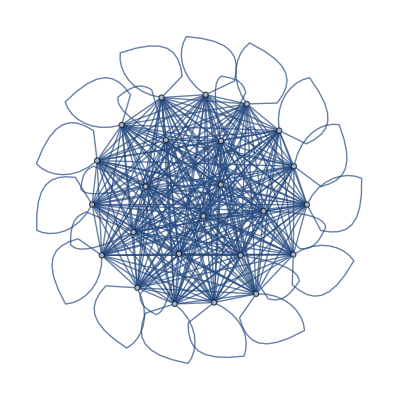

```mathematica
WeightedAdjacencyGraph[ss1]
```

```mathematica
ss2=solt.sol
```

{{1.08405+0. ⅈ,-4.17994+0. ⅈ,1.88726+0. ⅈ},{-4.17994+0. ⅈ,-7.54427+0. ⅈ,-2.87604+0. ⅈ},{1.88726+0. ⅈ,-2.87604+0. ⅈ,4.91578+0. ⅈ}}

```mathematica
Eigenvalues[ss2]//Chop
```

{-9.51511,7.03193,0.93875}

```mathematica
(* Cartan matrix from Killing vector solutions*)
```

```mathematica
cart=Table[2*sol[[i]].sol[[j]]/(sol[[i]].sol[[i]]),{i,24},{j,24}]//Chop
```

{{2.,0.831634+2.43637 ⅈ,1.21372-0.278277 ⅈ,0.176136+2.27769 ⅈ,1.69739-1.20736 ⅈ,0.0116518+2.20735 ⅈ,0.147035-0.157375 ⅈ,-0.317196+1.06577 ⅈ,0.575238-0.466204 ⅈ,-0.32211+1.13262 ⅈ,-0.592029+0.209569 ⅈ,-1.40124+0.383152 ⅈ,0.195966-4.09846 ⅈ,-3.49692+3.88886 ⅈ,-0.0812801-0.270754 ⅈ,-0.432241+0.490649 ⅈ,-0.314754+0.304966 ⅈ,-0.770794-0.182364 ⅈ,-0.787841+0.135483 ⅈ,-0.92839-0.0429577 ⅈ,-0.291833-0.750212 ⅈ,-1.49826+0.41152 ⅈ,-0.707042-1.18637 ⅈ,-1.60024+0.525358 ⅈ},{0.831634-2.43637 ⅈ,2.,0.176136-2.27769 ⅈ,1.21372+0.278277 ⅈ,0.0116518-2.20735 ⅈ,1.69739+1.20736 ⅈ,-0.317196-1.06577 ⅈ,0.147035+0.157375 ⅈ,-0.32211-1.13262 ⅈ,0.575238+0.466204 ⅈ,-1.40124-0.383152 ⅈ,-0.592029-0.209569 ⅈ,-3.49692-3.88886 ⅈ,0.195966+4.09846 ⅈ,-0.432241-0.490649 ⅈ,-0.0812801+0.270754 ⅈ,-0.770794+0.182364 ⅈ,-0.314754-0.304966 ⅈ,-0.92839+0.0429577 ⅈ,-0.787841-0.135483 ⅈ,-1.49826-0.41152 ⅈ,-0.291833+0.750212 ⅈ,-1.60024-0.525358 ⅈ,-0.707042+1.18637 ⅈ},{7.85194-0.328646 ⅈ,5.57677+13.2957 ⅈ,2.,2.21723+15.1426 ⅈ,7.53117-9.69466 ⅈ,3.67508+9.18292 ⅈ,-1.75454+0.773544 ⅈ,-1.20351+8.16582 ⅈ,2.35971-2.58765 ⅈ,-0.941461+5.76324 ⅈ,-2.73229+8.63819 ⅈ,-12.9431+6.33073 ⅈ,-8.32025-16.9819 ⅈ,-13.8766+28.3044 ⅈ,-0.99893-1.47697 ⅈ,-1.5138+2.84484 ⅈ,1.29062+4.56187 ⅈ,-7.80152-1.27787 ⅈ,-4.15217+4.242 ⅈ,-7.11544+2.2231 ⅈ,0.0895873-1.32342 ⅈ,-9.98301+2.24103 ⅈ,-4.92516-4.91966 ⅈ,-7.52489+4.32581 ⅈ},{5.57677-13.2957 ⅈ,7.85194+0.328646 ⅈ,2.21723-15.1426 ⅈ,2.,3.67508-9.18292 ⅈ,7.53117+9.69466 ⅈ,-1.20351-8.16582 ⅈ,-1.75454-0.773544 ⅈ,-0.941461-5.76324 ⅈ,2.35971+2.58765 ⅈ,-12.9431-6.33073 ⅈ,-2.73229-8.63819 ⅈ,-13.8766-28.3044 ⅈ,-8.32025+16.9819 ⅈ,-1.5138-2.84484 ⅈ,-0.99893+1.47697 ⅈ,-7.80152+1.27787 ⅈ,1.29062-4.56187 ⅈ,-7.11544-2.2231 ⅈ,-4.15217-4.242 ⅈ,-9.98301-2.24103 ⅈ,0.0895873+1.32342 ⅈ,-7.52489-4.32581 ⅈ,-4.92516+4.91966 ⅈ},{2.35772-0.0814709 ⅈ,0.172043+2.49408 ⅈ,1.92248-1.07576 ⅈ,-0.835481+1.56604 ⅈ,2.,-0.944185+3.6252 ⅈ,0.363917-0.657771 ⅈ,-1.03572+0.59612 ⅈ,0.372395-0.157029 ⅈ,-0.739047+1.57491 ⅈ,-2.02952-1.74677 ⅈ,-0.390881-1.33108 ⅈ,1.82317-6.10878 ⅈ,-5.682+2.29087 ⅈ,-0.24212+0.0623563 ⅈ,-0.960204+0.862723 ⅈ,-1.94621+0.134466 ⅈ,0.195794-0.160098 ⅈ,-1.52449-0.574156 ⅈ,-0.805517-0.690468 ⅈ,-1.5487-0.894191 ⅈ,-0.985984+0.541583 ⅈ,-0.874186-1.23279 ⅈ,-2.23099+0.599863 ⅈ},{0.172043-2.49408 ⅈ,2.35772+0.0814709 ⅈ,-0.835481-1.56604 ⅈ,1.92248+1.07576 ⅈ,-0.944185-3.6252 ⅈ,2.,-1.03572-0.59612 ⅈ,0.363917+0.657771 ⅈ,-0.739047-1.57491 ⅈ,0.372395+0.157029 ⅈ,-0.390881+1.33108 ⅈ,-2.02952+1.74677 ⅈ,-5.682-2.29087 ⅈ,1.82317+6.10878 ⅈ,-0.960204-0.862723 ⅈ,-0.24212-0.0623563 ⅈ,0.195794+0.160098 ⅈ,-1.94621-0.134466 ⅈ,-0.805517+0.690468 ⅈ,-1.52449+0.574156 ⅈ,-0.985984-0.541583 ⅈ,-1.5487+0.894191 ⅈ,-2.23099-0.599863 ⅈ,-0.874186+1.23279 ⅈ},{-0.83466-0.245666 ⅈ,0.708775-4.43582 ⅈ,1.07309+0.595749 ⅈ,2.46284-4.67418 ⅈ,-2.29486+1.38682 ⅈ,-0.0728542-4.26192 ⅈ,2.,2.62567-2.67197 ⅈ,0.329065-0.127333 ⅈ,1.50123-2.27012 ⅈ,4.68058-2.63638 ⅈ,5.67592+0.438095 ⅈ,3.44955+6.60963 ⅈ,8.34187-7.76582 ⅈ,1.15863-0.220131 ⅈ,1.62369-1.59546 ⅈ,2.02807-2.85596 ⅈ,2.56053+1.18685 ⅈ,3.38801-1.47962 ⅈ,3.55074-0.122125 ⅈ,1.84949-1.04557 ⅈ,3.37734-0.0266747 ⅈ,2.29924+0.976906 ⅈ,3.47183-1.6309 ⅈ},{0.708775+4.43582 ⅈ,-0.83466+0.245666 ⅈ,2.46284+4.67418 ⅈ,1.07309-0.595749 ⅈ,-0.0728542+4.26192 ⅈ,-2.29486-1.38682 ⅈ,2.62567+2.67197 ⅈ,2.,1.50123+2.27012 ⅈ,0.329065+0.127333 ⅈ,5.67592-0.438095 ⅈ,4.68058+2.63638 ⅈ,8.34187+7.76582 ⅈ,3.44955-6.60963 ⅈ,1.62369+1.59546 ⅈ,1.15863+0.220131 ⅈ,2.56053-1.18685 ⅈ,2.02807+2.85596 ⅈ,3.55074+0.122125 ⅈ,3.38801+1.47962 ⅈ,3.37734+0.0266747 ⅈ,1.84949+1.04557 ⅈ,3.47183+1.6309 ⅈ,2.29924-0.976906 ⅈ},{-9.90951-6.91397 ⅈ,6.68496-18.0158 ⅈ,-8.71423-2.46135 ⅈ,9.18618-11.9837 ⅈ,-5.55015-1.76252 ⅈ,17.582-17.8668 ⅈ,1.40113-0.26154 ⅈ,10.0516-4.45367 ⅈ,2.,12.5486-8.76052 ⅈ,7.08305+9.07509 ⅈ,6.36914+0.0861868 ⅈ,-16.6861+26.2272 ⅈ,38.0757-8.61672 ⅈ,6.85486-0.217658 ⅈ,12.0779-3.52713 ⅈ,12.3306+3.09098 ⅈ,7.20973-2.47723 ⅈ,10.5722+3.68058 ⅈ,8.76623+1.94025 ⅈ,8.96391+8.85809 ⅈ,15.1806-3.76797 ⅈ,7.93519+8.5177 ⅈ,19.4051-0.0990135 ⅈ},{6.68496+18.0158 ⅈ,-9.90951+6.91397 ⅈ,9.18618+11.9837 ⅈ,-8.71423+2.46135 ⅈ,17.582+17.8668 ⅈ,-5.55015+1.76252 ⅈ,10.0516+4.45367 ⅈ,1.40113+0.26154 ⅈ,12.5486+8.76052 ⅈ,2.,6.36914-0.0861868 ⅈ,7.08305-9.07509 ⅈ,38.0757+8.61672 ⅈ,-16.6861-26.2272 ⅈ,12.0779+3.52713 ⅈ,6.85486+0.217658 ⅈ,7.20973+2.47723 ⅈ,12.3306-3.09098 ⅈ,8.76623-1.94025 ⅈ,10.5722-3.68058 ⅈ,15.1806+3.76797 ⅈ,8.96391-8.85809 ⅈ,19.4051+0.0990135 ⅈ,7.93519-8.5177 ⅈ},{-0.331129+0.277475 ⅈ,0.732386-0.67985 ⅈ,0.229405+0.960485 ⅈ,1.46035-0.577655 ⅈ,-1.58344+0.371278 ⅈ,-0.122392-0.833669 ⅈ,0.360444+0.840744 ⅈ,0.96929+0.0130273 ⅈ,-0.358535+0.327017 ⅈ,0.259369+0.0694454 ⅈ,2.,1.63112+1.99173 ⅈ,0.0385045+2.99185 ⅈ,3.60928-0.536613 ⅈ,-0.181391+0.511097 ⅈ,0.159653+0.171708 ⅈ,0.67026-0.553847 ⅈ,0.0350705+1.59478 ⅈ,0.971188+0.385663 ⅈ,0.754799+1.09739 ⅈ,0.261266-0.0565424 ⅈ,0.370675+1.32942 ⅈ,-0.0392836+0.960233 ⅈ,0.663608+0.492893 ⅈ},{0.732386+0.67985 ⅈ,-0.331129-0.277475 ⅈ,1.46035+0.577655 ⅈ,0.229405-0.960485 ⅈ,-0.122392+0.833669 ⅈ,-1.58344-0.371278 ⅈ,0.96929-0.0130273 ⅈ,0.360444-0.840744 ⅈ,0.259369-0.0694454 ⅈ,-0.358535-0.327017 ⅈ,1.63112-1.99173 ⅈ,2.,3.60928+0.536613 ⅈ,0.0385045-2.99185 ⅈ,0.159653-0.171708 ⅈ,-0.181391-0.511097 ⅈ,0.0350705-1.59478 ⅈ,0.67026+0.553847 ⅈ,0.754799-1.09739 ⅈ,0.971188-0.385663 ⅈ,0.370675-1.32942 ⅈ,0.261266+0.0565424 ⅈ,0.663608-0.492893 ⅈ,-0.0392836-0.960233 ⅈ},{0.136485+0.642469 ⅈ,-0.834716+0.0640389 ⅈ,0.374585+0.299561 ⅈ,-0.741441-0.299183 ⅈ,0.471571+0.767773 ⅈ,-0.864723-0.0449975 ⅈ,0.284493-0.0796306 ⅈ,-0.266256-0.36477 ⅈ,0.253362+0.169656 ⅈ,-0.316514-0.215537 ⅈ,0.0606886-0.693613 ⅈ,0.366395-0.765995 ⅈ,2.,-1.25493-1.8904 ⅈ,0.21654-0.0652973 ⅈ,-0.0942926-0.245457 ⅈ,-0.15-0.35814 ⅈ,0.400454-0.272056 ⅈ,0.100295-0.527456 ⅈ,0.288198-0.494801 ⅈ,0.275401-0.271807 ⅈ,0.147623-0.575499 ⅈ,0.596993-0.302802 ⅈ,-0.0479914-0.712297 ⅈ},{-0.834716-0.0640389 ⅈ,0.136485-0.642469 ⅈ,-0.741441+0.299183 ⅈ,0.374585-0.299561 ⅈ,-0.864723+0.0449975 ⅈ,0.471571-0.767773 ⅈ,-0.266256+0.36477 ⅈ,0.284493+0.0796306 ⅈ,-0.316514+0.215537 ⅈ,0.253362-0.169656 ⅈ,0.366395+0.765995 ⅈ,0.0606886+0.693613 ⅈ,-1.25493+1.8904 ⅈ,2.,-0.0942926+0.245457 ⅈ,0.21654+0.0652973 ⅈ,0.400454+0.272056 ⅈ,-0.15+0.35814 ⅈ,0.288198+0.494801 ⅈ,0.100295+0.527456 ⅈ,0.147623+0.575499 ⅈ,0.275401+0.271807 ⅈ,-0.0479914+0.712297 ⅈ,0.596993+0.302802 ⅈ},{-0.931926+0.229511 ⅈ,0.52963-2.15593 ⅈ,-0.716016+0.638263 ⅈ,1.05962-1.37202 ⅈ,0.530094+0.529853 ⅈ,2.51644-2.93961 ⅈ,0.938447+0.318939 ⅈ,1.82977-0.558564 ⅈ,1.36358+0.420241 ⅈ,2.15443-1.48695 ⅈ,1.96132+1.82151 ⅈ,1.13032-0.247929 ⅈ,-0.0690644+4.79654 ⅈ,4.8995-2.66419 ⅈ,2.,2.47501-0.708407 ⅈ,2.87635+0.595161 ⅈ,1.69555-0.73239 ⅈ,2.43753+0.50444 ⅈ,2.03922+0.0875109 ⅈ,2.86208+1.48141 ⅈ,2.72259-1.35497 ⅈ,2.67589+1.10309 ⅈ,3.60957-0.762117 ⅈ},{0.52963+2.15593 ⅈ,-0.931926-0.229511 ⅈ,1.05962+1.37202 ⅈ,-0.716016-0.638263 ⅈ,2.51644+2.93961 ⅈ,0.530094-0.529853 ⅈ,1.82977+0.558564 ⅈ,0.938447-0.318939 ⅈ,2.15443+1.48695 ⅈ,1.36358-0.420241 ⅈ,1.13032+0.247929 ⅈ,1.96132-1.82151 ⅈ,4.8995+2.66419 ⅈ,-0.0690644-4.79654 ⅈ,2.47501+0.708407 ⅈ,2.,1.69555+0.73239 ⅈ,2.87635-0.595161 ⅈ,2.03922-0.0875109 ⅈ,2.43753-0.50444 ⅈ,2.72259+1.35497 ⅈ,2.86208-1.48141 ⅈ,3.60957+0.762117 ⅈ,2.67589-1.10309 ⅈ},{-3.38367-1.94422 ⅈ,6.49363+2.75257 ⅈ,-4.94436+4.50493 ⅈ,8.8492+6.78946 ⅈ,-12.3169-9.14018 ⅈ,0.647384-1.88013 ⅈ,-5.55476+5.36242 ⅈ,1.63519+6.00196 ⅈ,-6.72672-1.69237 ⅈ,-2.62749+3.22484 ⅈ,6.47522+9.20564 ⅈ,-6.06232+19.7384 ⅈ,-19.7288+8.79135 ⅈ,15.1595+22.2584 ⅈ,-7.64273+0.966566 ⅈ,-4.29744+2.23531 ⅈ,2.,-12.5562+8.74974 ⅈ,-1.54908+6.72099 ⅈ,-6.39679+9.55344 ⅈ,-3.25741-1.00308 ⅈ,-10.3908+10.3579 ⅈ,-10.6546+2.89014 ⅈ,-5.03444+7.20612 ⅈ},{6.49363-2.75257 ⅈ,-3.38367+1.94422 ⅈ,8.8492-6.78946 ⅈ,-4.94436-4.50493 ⅈ,0.647384+1.88013 ⅈ,-12.3169+9.14018 ⅈ,1.63519-6.00196 ⅈ,-5.55476-5.36242 ⅈ,-2.62749-3.22484 ⅈ,-6.72672+1.69237 ⅈ,-6.06232-19.7384 ⅈ,6.47522-9.20564 ⅈ,15.1595-22.2584 ⅈ,-19.7288-8.79135 ⅈ,-4.29744-2.23531 ⅈ,-7.64273-0.966566 ⅈ,-12.5562-8.74974 ⅈ,2.,-6.39679-9.55344 ⅈ,-1.54908-6.72099 ⅈ,-10.3908-10.3579 ⅈ,-3.25741+1.00308 ⅈ,-5.03444-7.20612 ⅈ,-10.6546-2.89014 ⅈ},{-0.588843+1.22281 ⅈ,-0.134017-1.57217 ⅈ,0.563361+1.49412 ⅈ,0.867873-1.80782 ⅈ,-0.940912+2.25342 ⅈ,-0.259207-1.56913 ⅈ,1.2154+0.967903 ⅈ,1.33148-0.675704 ⅈ,0.384192+1.09945 ⅈ,0.802535-0.477955 ⅈ,2.51883-0.553903 ⅈ,3.21742+0.673842 ⅈ,2.76353+4.97897 ⅈ,4.1285-4.45413 ⅈ,0.891025+0.869161 ⅈ,1.02016-0.0321635 ⅈ,1.18669-0.566695 ⅈ,1.72865+1.34803 ⅈ,2.,2.17419+0.649138 ⅈ,1.33414+0.541314 ⅈ,2.14686+0.484815 ⅈ,1.77117+1.50618 ⅈ,2.1571-0.315318 ⅈ},{-0.134017+1.57217 ⅈ,-0.588843-1.22281 ⅈ,0.867873+1.80782 ⅈ,0.563361-1.49412 ⅈ,-0.259207+1.56913 ⅈ,-0.940912-2.25342 ⅈ,1.33148+0.675704 ⅈ,1.2154-0.967903 ⅈ,0.802535+0.477955 ⅈ,0.384192-1.09945 ⅈ,3.21742-0.673842 ⅈ,2.51883+0.553903 ⅈ,4.1285+4.45413 ⅈ,2.76353-4.97897 ⅈ,1.02016+0.0321635 ⅈ,0.891025-0.869161 ⅈ,1.72865-1.34803 ⅈ,1.18669+0.566695 ⅈ,2.17419-0.649138 ⅈ,2.,2.14686-0.484815 ⅈ,1.33414-0.541314 ⅈ,2.1571+0.315318 ⅈ,1.77117-1.50618 ⅈ},{-0.332654+1.41352 ⅈ,-2.73997-0.590576 ⅈ,-0.177149+0.335213 ⅈ,-2.74856-0.998984 ⅈ,2.44016+1.46938 ⅈ,-0.922049-1.53634 ⅈ,0.498135-0.807433 ⅈ,-0.74029-1.31401 ⅈ,1.3873+0.127027 ⅈ,-0.16056-1.72157 ⅈ,-0.514715-0.475902 ⅈ,-0.50895-3.58331 ⅈ,4.34657+0.350187 ⅈ,-3.57905-5.6587 ⅈ,1.46763-0.882174 ⅈ,0.711845-1.45061 ⅈ,0.638577-0.262703 ⅈ,1.28853-2.67852 ⅈ,0.551047-1.42713 ⅈ,0.782576-2.20376 ⅈ,2.,1.01069-3.60722 ⅈ,2.7066-1.19834 ⅈ,1.03295-2.90176 ⅈ},{-2.73997+0.590576 ⅈ,-0.332654-1.41352 ⅈ,-2.74856+0.998984 ⅈ,-0.177149-0.335213 ⅈ,-0.922049+1.53634 ⅈ,2.44016-1.46938 ⅈ,-0.74029+1.31401 ⅈ,0.498135+0.807433 ⅈ,-0.16056+1.72157 ⅈ,1.3873-0.127027 ⅈ,-0.50895+3.58331 ⅈ,-0.514715+0.475902 ⅈ,-3.57905+5.6587 ⅈ,4.34657-0.350187 ⅈ,0.711845+1.45061 ⅈ,1.46763+0.882174 ⅈ,1.28853+2.67852 ⅈ,0.638577+0.262703 ⅈ,0.782576+2.20376 ⅈ,0.551047+1.42713 ⅈ,1.01069+3.60722 ⅈ,2.,1.03295+2.90176 ⅈ,2.7066+1.19834 ⅈ},{-0.673785+1.3496 ⅈ,-1.45346-1.12764 ⅈ,-0.0373293+1.20415 ⅈ,-0.750135-1.30138 ⅈ,0.289619+1.42837 ⅈ,-0.830075-2.06752 ⅈ,0.645918+0.19745 ⅈ,0.322858-0.985542 ⅈ,0.671851+0.394566 ⅈ,0.0872046-1.29586 ⅈ,1.50334-0.261409 ⅈ,1.04209-0.797932 ⅈ,3.22059+3.2387 ⅈ,0.741355-4.81443 ⅈ,0.90671-0.211784 ⅈ,0.670971-0.97893 ⅈ,1.15051-0.714142 ⅈ,0.921005-0.5607 ⅈ,1.32348-0.696877 ⅈ,1.25422-0.627583 ⅈ,1.79186-0.0330252 ⅈ,1.05723-1.53626 ⅈ,2.,1.4118-1.77631 ⅈ},{-1.45346+1.12764 ⅈ,-0.673785-1.3496 ⅈ,-0.750135+1.30138 ⅈ,-0.0373293-1.20415 ⅈ,-0.830075+2.06752 ⅈ,0.289619-1.42837 ⅈ,0.322858+0.985542 ⅈ,0.645918-0.19745 ⅈ,0.0872046+1.29586 ⅈ,0.671851-0.394566 ⅈ,1.04209+0.797932 ⅈ,1.50334+0.261409 ⅈ,0.741355+4.81443 ⅈ,3.22059-3.2387 ⅈ,0.670971+0.97893 ⅈ,0.90671+0.211784 ⅈ,0.921005+0.5607 ⅈ,1.15051+0.714142 ⅈ,1.25422+0.627583 ⅈ,1.32348+0.696877 ⅈ,1.05723+1.53626 ⅈ,1.79186+0.0330252 ⅈ,1.4118+1.77631 ⅈ,2.}}

```mathematica
TableForm[cart]
```

2. | 0.831634+2.43637 ⅈ | 1.21372-0.278277 ⅈ | 0.176136+2.27769 ⅈ | 1.69739-1.20736 ⅈ | 0.0116518+2.20735 ⅈ | 0.147035-0.157375 ⅈ | -0.317196+1.06577 ⅈ | 0.575238-0.466204 ⅈ | -0.32211+1.13262 ⅈ | -0.592029+0.209569 ⅈ | -1.40124+0.383152 ⅈ | 0.195966-4.09846 ⅈ | -3.49692+3.88886 ⅈ | -0.0812801-0.270754 ⅈ | -0.432241+0.490649 ⅈ | -0.314754+0.304966 ⅈ | -0.770794-0.182364 ⅈ | -0.787841+0.135483 ⅈ | -0.92839-0.0429577 ⅈ | -0.291833-0.750212 ⅈ | -1.49826+0.41152 ⅈ | -0.707042-1.18637 ⅈ | -1.60024+0.525358 ⅈ
0.831634-2.43637 ⅈ | 2. | 0.176136-2.27769 ⅈ | 1.21372+0.278277 ⅈ | 0.0116518-2.20735 ⅈ | 1.69739+1.20736 ⅈ | -0.317196-1.06577 ⅈ | 0.147035+0.157375 ⅈ | -0.32211-1.13262 ⅈ | 0.575238+0.466204 ⅈ | -1.40124-0.383152 ⅈ | -0.592029-0.209569 ⅈ | -3.49692-3.88886 ⅈ | 0.195966+4.09846 ⅈ | -0.432241-0.490649 ⅈ | -0.0812801+0.270754 ⅈ | -0.770794+0.182364 ⅈ | -0.314754-0.304966 ⅈ | -0.92839+0.0429577 ⅈ | -0.787841-0.135483 ⅈ | -1.49826-0.41152 ⅈ | -0.291833+0.750212 ⅈ | -1.60024-0.525358 ⅈ | -0.707042+1.18637 ⅈ
7.85194-0.328646 ⅈ | 5.57677+13.2957 ⅈ | 2. | 2.21723+15.1426 ⅈ | 7.53117-9.69466 ⅈ | 3.67508+9.18292 ⅈ | -1.75454+0.773544 ⅈ | -1.20351+8.16582 ⅈ | 2.35971-2.58765 ⅈ | -0.941461+5.76324 ⅈ | -2.73229+8.63819 ⅈ | -12.9431+6.33073 ⅈ | -8.32025-16.9819 ⅈ | -13.8766+28.3044 ⅈ | -0.99893-1.47697 ⅈ | -1.5138+2.84484 ⅈ | 1.29062+4.56187 ⅈ | -7.80152-1.27787 ⅈ | -4.15217+4.242 ⅈ | -7.11544+2.2231 ⅈ | 0.0895873-1.32342 ⅈ | -9.98301+2.24103 ⅈ | -4.92516-4.91966 ⅈ | -7.52489+4.32581 ⅈ
5.57677-13.2957 ⅈ | 7.85194+0.328646 ⅈ | 2.21723-15.1426 ⅈ | 2. | 3.67508-9.18292 ⅈ | 7.53117+9.69466 ⅈ | -1.20351-8.16582 ⅈ | -1.75454-0.773544 ⅈ | -0.941461-5.76324 ⅈ | 2.35971+2.58765 ⅈ | -12.9431-6.33073 ⅈ | -2.73229-8.63819 ⅈ | -13.8766-28.3044 ⅈ | -8.32025+16.9819 ⅈ | -1.5138-2.84484 ⅈ | -0.99893+1.47697 ⅈ | -7.80152+1.27787 ⅈ | 1.29062-4.56187 ⅈ | -7.11544-2.2231 ⅈ | -4.15217-4.242 ⅈ | -9.98301-2.24103 ⅈ | 0.0895873+1.32342 ⅈ | -7.52489-4.32581 ⅈ | -4.92516+4.91966 ⅈ
2.35772-0.0814709 ⅈ | 0.172043+2.49408 ⅈ | 1.92248-1.07576 ⅈ | -0.835481+1.56604 ⅈ | 2. | -0.944185+3.6252 ⅈ | 0.363917-0.657771 ⅈ | -1.03572+0.59612 ⅈ | 0.372395-0.157029 ⅈ | -0.739047+1.57491 ⅈ | -2.02952-1.74677 ⅈ | -0.390881-1.33108 ⅈ | 1.82317-6.10878 ⅈ | -5.682+2.29087 ⅈ | -0.24212+0.0623563 ⅈ | -0.960204+0.862723 ⅈ | -1.94621+0.134466 ⅈ | 0.195794-0.160098 ⅈ | -1.52449-0.574156 ⅈ | -0.805517-0.690468 ⅈ | -1.5487-0.894191 ⅈ | -0.985984+0.541583 ⅈ | -0.874186-1.23279 ⅈ | -2.23099+0.599863 ⅈ
0.172043-2.49408 ⅈ | 2.35772+0.0814709 ⅈ | -0.835481-1.56604 ⅈ | 1.92248+1.07576 ⅈ | -0.944185-3.6252 ⅈ | 2. | -1.03572-0.59612 ⅈ | 0.363917+0.657771 ⅈ | -0.739047-1.57491 ⅈ | 0.372395+0.157029 ⅈ | -0.390881+1.33108 ⅈ | -2.02952+1.74677 ⅈ | -5.682-2.29087 ⅈ | 1.82317+6.10878 ⅈ | -0.960204-0.862723 ⅈ | -0.24212-0.0623563 ⅈ | 0.195794+0.160098 ⅈ | -1.94621-0.134466 ⅈ | -0.805517+0.690468 ⅈ | -1.52449+0.574156 ⅈ | -0.985984-0.541583 ⅈ | -1.5487+0.894191 ⅈ | -2.23099-0.599863 ⅈ | -0.874186+1.23279 ⅈ
-0.83466-0.245666 ⅈ | 0.708775-4.43582 ⅈ | 1.07309+0.595749 ⅈ | 2.46284-4.67418 ⅈ | -2.29486+1.38682 ⅈ | -0.0728542-4.26192 ⅈ | 2. | 2.62567-2.67197 ⅈ | 0.329065-0.127333 ⅈ | 1.50123-2.27012 ⅈ | 4.68058-2.63638 ⅈ | 5.67592+0.438095 ⅈ | 3.44955+6.60963 ⅈ | 8.34187-7.76582 ⅈ | 1.15863-0.220131 ⅈ | 1.62369-1.59546 ⅈ | 2.02807-2.85596 ⅈ | 2.56053+1.18685 ⅈ | 3.38801-1.47962 ⅈ | 3.55074-0.122125 ⅈ | 1.84949-1.04557 ⅈ | 3.37734-0.0266747 ⅈ | 2.29924+0.976906 ⅈ | 3.47183-1.6309 ⅈ
0.708775+4.43582 ⅈ | -0.83466+0.245666 ⅈ | 2.46284+4.67418 ⅈ | 1.07309-0.595749 ⅈ | -0.0728542+4.26192 ⅈ | -2.29486-1.38682 ⅈ | 2.62567+2.67197 ⅈ | 2. | 1.50123+2.27012 ⅈ | 0.329065+0.127333 ⅈ | 5.67592-0.438095 ⅈ | 4.68058+2.63638 ⅈ | 8.34187+7.76582 ⅈ | 3.44955-6.60963 ⅈ | 1.62369+1.59546 ⅈ | 1.15863+0.220131 ⅈ | 2.56053-1.18685 ⅈ | 2.02807+2.85596 ⅈ | 3.55074+0.122125 ⅈ | 3.38801+1.47962 ⅈ | 3.37734+0.0266747 ⅈ | 1.84949+1.04557 ⅈ | 3.47183+1.6309 ⅈ | 2.29924-0.976906 ⅈ
-9.90951-6.91397 ⅈ | 6.68496-18.0158 ⅈ | -8.71423-2.46135 ⅈ | 9.18618-11.9837 ⅈ | -5.55015-1.76252 ⅈ | 17.582-17.8668 ⅈ | 1.40113-0.26154 ⅈ | 10.0516-4.45367 ⅈ | 2. | 12.5486-8.76052 ⅈ | 7.08305+9.07509 ⅈ | 6.36914+0.0861868 ⅈ | -16.6861+26.2272 ⅈ | 38.0757-8.61672 ⅈ | 6.85486-0.217658 ⅈ | 12.0779-3.52713 ⅈ | 12.3306+3.09098 ⅈ | 7.20973-2.47723 ⅈ | 10.5722+3.68058 ⅈ | 8.76623+1.94025 ⅈ | 8.96391+8.85809 ⅈ | 15.1806-3.76797 ⅈ | 7.93519+8.5177 ⅈ | 19.4051-0.0990135 ⅈ
6.68496+18.0158 ⅈ | -9.90951+6.91397 ⅈ | 9.18618+11.9837 ⅈ | -8.71423+2.46135 ⅈ | 17.582+17.8668 ⅈ | -5.55015+1.76252 ⅈ | 10.0516+4.45367 ⅈ | 1.40113+0.26154 ⅈ | 12.5486+8.76052 ⅈ | 2. | 6.36914-0.0861868 ⅈ | 7.08305-9.07509 ⅈ | 38.0757+8.61672 ⅈ | -16.6861-26.2272 ⅈ | 12.0779+3.52713 ⅈ | 6.85486+0.217658 ⅈ | 7.20973+2.47723 ⅈ | 12.3306-3.09098 ⅈ | 8.76623-1.94025 ⅈ | 10.5722-3.68058 ⅈ | 15.1806+3.76797 ⅈ | 8.96391-8.85809 ⅈ | 19.4051+0.0990135 ⅈ | 7.93519-8.5177 ⅈ
-0.331129+0.277475 ⅈ | 0.732386-0.67985 ⅈ | 0.229405+0.960485 ⅈ | 1.46035-0.577655 ⅈ | -1.58344+0.371278 ⅈ | -0.122392-0.833669 ⅈ | 0.360444+0.840744 ⅈ | 0.96929+0.0130273 ⅈ | -0.358535+0.327017 ⅈ | 0.259369+0.0694454 ⅈ | 2. | 1.63112+1.99173 ⅈ | 0.0385045+2.99185 ⅈ | 3.60928-0.536613 ⅈ | -0.181391+0.511097 ⅈ | 0.159653+0.171708 ⅈ | 0.67026-0.553847 ⅈ | 0.0350705+1.59478 ⅈ | 0.971188+0.385663 ⅈ | 0.754799+1.09739 ⅈ | 0.261266-0.0565424 ⅈ | 0.370675+1.32942 ⅈ | -0.0392836+0.960233 ⅈ | 0.663608+0.492893 ⅈ
0.732386+0.67985 ⅈ | -0.331129-0.277475 ⅈ | 1.46035+0.577655 ⅈ | 0.229405-0.960485 ⅈ | -0.122392+0.833669 ⅈ | -1.58344-0.371278 ⅈ | 0.96929-0.0130273 ⅈ | 0.360444-0.840744 ⅈ | 0.259369-0.0694454 ⅈ | -0.358535-0.327017 ⅈ | 1.63112-1.99173 ⅈ | 2. | 3.60928+0.536613 ⅈ | 0.0385045-2.99185 ⅈ | 0.159653-0.171708 ⅈ | -0.181391-0.511097 ⅈ | 0.0350705-1.59478 ⅈ | 0.67026+0.553847 ⅈ | 0.754799-1.09739 ⅈ | 0.971188-0.385663 ⅈ | 0.370675-1.32942 ⅈ | 0.261266+0.0565424 ⅈ | 0.663608-0.492893 ⅈ | -0.0392836-0.960233 ⅈ
0.136485+0.642469 ⅈ | -0.834716+0.0640389 ⅈ | 0.374585+0.299561 ⅈ | -0.741441-0.299183 ⅈ | 0.471571+0.767773 ⅈ | -0.864723-0.0449975 ⅈ | 0.284493-0.0796306 ⅈ | -0.266256-0.36477 ⅈ | 0.253362+0.169656 ⅈ | -0.316514-0.215537 ⅈ | 0.0606886-0.693613 ⅈ | 0.366395-0.765995 ⅈ | 2. | -1.25493-1.8904 ⅈ | 0.21654-0.0652973 ⅈ | -0.0942926-0.245457 ⅈ | -0.15-0.35814 ⅈ | 0.400454-0.272056 ⅈ | 0.100295-0.527456 ⅈ | 0.288198-0.494801 ⅈ | 0.275401-0.271807 ⅈ | 0.147623-0.575499 ⅈ | 0.596993-0.302802 ⅈ | -0.0479914-0.712297 ⅈ
-0.834716-0.0640389 ⅈ | 0.136485-0.642469 ⅈ | -0.741441+0.299183 ⅈ | 0.374585-0.299561 ⅈ | -0.864723+0.0449975 ⅈ | 0.471571-0.767773 ⅈ | -0.266256+0.36477 ⅈ | 0.284493+0.0796306 ⅈ | -0.316514+0.215537 ⅈ | 0.253362-0.169656 ⅈ | 0.366395+0.765995 ⅈ | 0.0606886+0.693613 ⅈ | -1.25493+1.8904 ⅈ | 2. | -0.0942926+0.245457 ⅈ | 0.21654+0.0652973 ⅈ | 0.400454+0.272056 ⅈ | -0.15+0.35814 ⅈ | 0.288198+0.494801 ⅈ | 0.100295+0.527456 ⅈ | 0.147623+0.575499 ⅈ | 0.275401+0.271807 ⅈ | -0.0479914+0.712297 ⅈ | 0.596993+0.302802 ⅈ
-0.931926+0.229511 ⅈ | 0.52963-2.15593 ⅈ | -0.716016+0.638263 ⅈ | 1.05962-1.37202 ⅈ | 0.530094+0.529853 ⅈ | 2.51644-2.93961 ⅈ | 0.938447+0.318939 ⅈ | 1.82977-0.558564 ⅈ | 1.36358+0.420241 ⅈ | 2.15443-1.48695 ⅈ | 1.96132+1.82151 ⅈ | 1.13032-0.247929 ⅈ | -0.0690644+4.79654 ⅈ | 4.8995-2.66419 ⅈ | 2. | 2.47501-0.708407 ⅈ | 2.87635+0.595161 ⅈ | 1.69555-0.73239 ⅈ | 2.43753+0.50444 ⅈ | 2.03922+0.0875109 ⅈ | 2.86208+1.48141 ⅈ | 2.72259-1.35497 ⅈ | 2.67589+1.10309 ⅈ | 3.60957-0.762117 ⅈ
0.52963+2.15593 ⅈ | -0.931926-0.229511 ⅈ | 1.05962+1.37202 ⅈ | -0.716016-0.638263 ⅈ | 2.51644+2.93961 ⅈ | 0.530094-0.529853 ⅈ | 1.82977+0.558564 ⅈ | 0.938447-0.318939 ⅈ | 2.15443+1.48695 ⅈ | 1.36358-0.420241 ⅈ | 1.13032+0.247929 ⅈ | 1.96132-1.82151 ⅈ | 4.8995+2.66419 ⅈ | -0.0690644-4.79654 ⅈ | 2.47501+0.708407 ⅈ | 2. | 1.69555+0.73239 ⅈ | 2.87635-0.595161 ⅈ | 2.03922-0.0875109 ⅈ | 2.43753-0.50444 ⅈ | 2.72259+1.35497 ⅈ | 2.86208-1.48141 ⅈ | 3.60957+0.762117 ⅈ | 2.67589-1.10309 ⅈ
-3.38367-1.94422 ⅈ | 6.49363+2.75257 ⅈ | -4.94436+4.50493 ⅈ | 8.8492+6.78946 ⅈ | -12.3169-9.14018 ⅈ | 0.647384-1.88013 ⅈ | -5.55476+5.36242 ⅈ | 1.63519+6.00196 ⅈ | -6.72672-1.69237 ⅈ | -2.62749+3.22484 ⅈ | 6.47522+9.20564 ⅈ | -6.06232+19.7384 ⅈ | -19.7288+8.79135 ⅈ | 15.1595+22.2584 ⅈ | -7.64273+0.966566 ⅈ | -4.29744+2.23531 ⅈ | 2. | -12.5562+8.74974 ⅈ | -1.54908+6.72099 ⅈ | -6.39679+9.55344 ⅈ | -3.25741-1.00308 ⅈ | -10.3908+10.3579 ⅈ | -10.6546+2.89014 ⅈ | -5.03444+7.20612 ⅈ
6.49363-2.75257 ⅈ | -3.38367+1.94422 ⅈ | 8.8492-6.78946 ⅈ | -4.94436-4.50493 ⅈ | 0.647384+1.88013 ⅈ | -12.3169+9.14018 ⅈ | 1.63519-6.00196 ⅈ | -5.55476-5.36242 ⅈ | -2.62749-3.22484 ⅈ | -6.72672+1.69237 ⅈ | -6.06232-19.7384 ⅈ | 6.47522-9.20564 ⅈ | 15.1595-22.2584 ⅈ | -19.7288-8.79135 ⅈ | -4.29744-2.23531 ⅈ | -7.64273-0.966566 ⅈ | -12.5562-8.74974 ⅈ | 2. | -6.39679-9.55344 ⅈ | -1.54908-6.72099 ⅈ | -10.3908-10.3579 ⅈ | -3.25741+1.00308 ⅈ | -5.03444-7.20612 ⅈ | -10.6546-2.89014 ⅈ
-0.588843+1.22281 ⅈ | -0.134017-1.57217 ⅈ | 0.563361+1.49412 ⅈ | 0.867873-1.80782 ⅈ | -0.940912+2.25342 ⅈ | -0.259207-1.56913 ⅈ | 1.2154+0.967903 ⅈ | 1.33148-0.675704 ⅈ | 0.384192+1.09945 ⅈ | 0.802535-0.477955 ⅈ | 2.51883-0.553903 ⅈ | 3.21742+0.673842 ⅈ | 2.76353+4.97897 ⅈ | 4.1285-4.45413 ⅈ | 0.891025+0.869161 ⅈ | 1.02016-0.0321635 ⅈ | 1.18669-0.566695 ⅈ | 1.72865+1.34803 ⅈ | 2. | 2.17419+0.649138 ⅈ | 1.33414+0.541314 ⅈ | 2.14686+0.484815 ⅈ | 1.77117+1.50618 ⅈ | 2.1571-0.315318 ⅈ
-0.134017+1.57217 ⅈ | -0.588843-1.22281 ⅈ | 0.867873+1.80782 ⅈ | 0.563361-1.49412 ⅈ | -0.259207+1.56913 ⅈ | -0.940912-2.25342 ⅈ | 1.33148+0.675704 ⅈ | 1.2154-0.967903 ⅈ | 0.802535+0.477955 ⅈ | 0.384192-1.09945 ⅈ | 3.21742-0.673842 ⅈ | 2.51883+0.553903 ⅈ | 4.1285+4.45413 ⅈ | 2.76353-4.97897 ⅈ | 1.02016+0.0321635 ⅈ | 0.891025-0.869161 ⅈ | 1.72865-1.34803 ⅈ | 1.18669+0.566695 ⅈ | 2.17419-0.649138 ⅈ | 2. | 2.14686-0.484815 ⅈ | 1.33414-0.541314 ⅈ | 2.1571+0.315318 ⅈ | 1.77117-1.50618 ⅈ
-0.332654+1.41352 ⅈ | -2.73997-0.590576 ⅈ | -0.177149+0.335213 ⅈ | -2.74856-0.998984 ⅈ | 2.44016+1.46938 ⅈ | -0.922049-1.53634 ⅈ | 0.498135-0.807433 ⅈ | -0.74029-1.31401 ⅈ | 1.3873+0.127027 ⅈ | -0.16056-1.72157 ⅈ | -0.514715-0.475902 ⅈ | -0.50895-3.58331 ⅈ | 4.34657+0.350187 ⅈ | -3.57905-5.6587 ⅈ | 1.46763-0.882174 ⅈ | 0.711845-1.45061 ⅈ | 0.638577-0.262703 ⅈ | 1.28853-2.67852 ⅈ | 0.551047-1.42713 ⅈ | 0.782576-2.20376 ⅈ | 2. | 1.01069-3.60722 ⅈ | 2.7066-1.19834 ⅈ | 1.03295-2.90176 ⅈ
-2.73997+0.590576 ⅈ | -0.332654-1.41352 ⅈ | -2.74856+0.998984 ⅈ | -0.177149-0.335213 ⅈ | -0.922049+1.53634 ⅈ | 2.44016-1.46938 ⅈ | -0.74029+1.31401 ⅈ | 0.498135+0.807433 ⅈ | -0.16056+1.72157 ⅈ | 1.3873-0.127027 ⅈ | -0.50895+3.58331 ⅈ | -0.514715+0.475902 ⅈ | -3.57905+5.6587 ⅈ | 4.34657-0.350187 ⅈ | 0.711845+1.45061 ⅈ | 1.46763+0.882174 ⅈ | 1.28853+2.67852 ⅈ | 0.638577+0.262703 ⅈ | 0.782576+2.20376 ⅈ | 0.551047+1.42713 ⅈ | 1.01069+3.60722 ⅈ | 2. | 1.03295+2.90176 ⅈ | 2.7066+1.19834 ⅈ
-0.673785+1.3496 ⅈ | -1.45346-1.12764 ⅈ | -0.0373293+1.20415 ⅈ | -0.750135-1.30138 ⅈ | 0.289619+1.42837 ⅈ | -0.830075-2.06752 ⅈ | 0.645918+0.19745 ⅈ | 0.322858-0.985542 ⅈ | 0.671851+0.394566 ⅈ | 0.0872046-1.29586 ⅈ | 1.50334-0.261409 ⅈ | 1.04209-0.797932 ⅈ | 3.22059+3.2387 ⅈ | 0.741355-4.81443 ⅈ | 0.90671-0.211784 ⅈ | 0.670971-0.97893 ⅈ | 1.15051-0.714142 ⅈ | 0.921005-0.5607 ⅈ | 1.32348-0.696877 ⅈ | 1.25422-0.627583 ⅈ | 1.79186-0.0330252 ⅈ | 1.05723-1.53626 ⅈ | 2. | 1.4118-1.77631 ⅈ
-1.45346+1.12764 ⅈ | -0.673785-1.3496 ⅈ | -0.750135+1.30138 ⅈ | -0.0373293-1.20415 ⅈ | -0.830075+2.06752 ⅈ | 0.289619-1.42837 ⅈ | 0.322858+0.985542 ⅈ | 0.645918-0.19745 ⅈ | 0.0872046+1.29586 ⅈ | 0.671851-0.394566 ⅈ | 1.04209+0.797932 ⅈ | 1.50334+0.261409 ⅈ | 0.741355+4.81443 ⅈ | 3.22059-3.2387 ⅈ | 0.670971+0.97893 ⅈ | 0.90671+0.211784 ⅈ | 0.921005+0.5607 ⅈ | 1.15051+0.714142 ⅈ | 1.25422+0.627583 ⅈ | 1.32348+0.696877 ⅈ | 1.05723+1.53626 ⅈ | 1.79186+0.0330252 ⅈ | 1.4118+1.77631 ⅈ | 2.

```mathematica
Det[cart]//Chop
```

General::munfl: -(0.00118122-0.00500235 ⅈ)/(1123558209288947442330815744243140458511235611838941607958938007235829223784381«149»30092119569408801702322709406917786643639996702871154982269052209770601514008576) is too small to represent as a normalized machine number; precision may be lost.

0

```mathematica
Tr[cart]
```

48.

```mathematica
(* trace suggests an higher symmetry SU(7) as father of the dark field*)
```

```mathematica
ExpandAll[(CharacteristicPolynomial[cart,x]//Chop)/x^21]
```

-3920.+756. x-48. x^2+x^3

```mathematica
(* symmetry breaking: SU(5)->21 SO(7) zero states: 3 SU(2) energy carrying states*)
```

```mathematica
Eigenvalues[cart]//Chop
```

{20.,14.,14.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
WeightedAdjacencyGraph[cart]
```

-Graphics-